```mathematica
SetOptions[EvaluationNotebook[],{"ShowGroupOpener"->True}]
```

# ee > ZH for CLIC and ILC

Marion Thomas 7/11/24

### Setting everything up

```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Get["FeynCalc`"];
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to correctly cite this work.

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,0,0,SMP["m_Z"],SMP["m_H"]];

(*To match amplitudes with smeftatnlo*)
mg5Num={
SMP["m_W"]->79.824399999999997,
ee0->0.31345063981313520,
cw0->0.87538656571726847,
sw0->0.48342358295983689,
Lambda->1000,
SMP["m_Z"]->91.1876,
SMP["m_H"]->125,
vev0->246.22056907348588
};
tSUB=t->SMP["m_H"]^2/2+(-s+SMP["m_Z"]^2+cθ*Sqrt[SMP["m_H"]^4+(s-SMP["m_Z"]^2)^2-2*SMP["m_H"]^2*(s+SMP["m_Z"]^2)])/2;
costhetaSUB=cθ->z;

swsub={sw0->Sqrt[1-cw0^2]};
inputsubs={ee0->Sqrt[4*Pi*aEW],cw0->SMP["m_W"]/SMP["m_Z"],vev0->1/Sqrt[Sqrt[2]*GF]};
aEWsub={aEW->Sqrt[2]*SMP["m_W"]^2*(1-SMP["m_W"]^2/SMP["m_Z"]^2)*GF/Pi};
TurnOffEFT={cpBB->0,cpW->0,cpDC->0,c3pl1->0,cpl1->0,cpe->0,cdp->0,cpWB->0,c3pl2->0,cll->0, OpB->0,OpW->0,OpD->0,O3pl1->0,Opl1->0,Ope->0,Opd->0,OpWB->0,O3pl2->0,Oll->0,Obp->0,OtG->0,OpG->0,Otp->0, Opdi->0, O3pl3->0, Opta->0, OpQM->0,Opui->0,Otap->0, Opmu->0, OtZ->0, Ocp->0, Opl3->0, OtW->0, OpqMi->0, O3pQ3->0,Opt->0, Opl2->0,O3pq->0};
WilsonCoeffs={cpBB,cpW,cpDC,c3pl1,cpl1,cpe,cdp,cpWB,c3pl2,cll};
coeffsquares=TensorProduct[WilsonCoeffs,WilsonCoeffs]//Flatten//DeleteDuplicates;
WilsonCoeffsTOT=Join[WilsonCoeffs,coeffsquares]

(* mw scheme for predictions*)
inputNumSub={
GF->1.1663787*10^-5,
SMP["m_Z"]->91.1876,
SMP["m_W"]->80.387,
SMP["m_H"]->125,
Lambda->1000
};
gevm2topb=(1/(2.56819×10^−9));

ElectronPolarised={
DiracGamma[6].Spinor[Momentum[p1],a_,b_]:>DiracGamma[6].Spinor[Momentum[p1],a,b]*Sqrt[fR["e-"]],
DiracGamma[7].Spinor[Momentum[p1],a_,b_]:>DiracGamma[7].Spinor[Momentum[p1],a,b]*Sqrt[fL["e-"]]
};
PositronPolarised={
Spinor[-Momentum[p2],a_,b_].c_ .DiracGamma[6]:>Sqrt[fL["e+"]]*(Spinor[-Momentum[p2],a,b].c.DiracGamma[6]),
Spinor[-Momentum[p2],a_,b_].c_ .DiracGamma[7]:>Sqrt[fR["e+"]]*(Spinor[-Momentum[p2],a,b].c.DiracGamma[7])}

(*See page 112 of 2203.07622*)
PickPolarisations[amp_,Pe_,Pp_]:=(
Return[amp/.fR["e-"]->1-fL["e-"]/.fL["e-"]->(1-Pe)/2/.fR["e+"]->1-fL["e+"]/.fL["e+"]->(1-Pp)/2]);

ToSmefitFormat={cpWB->OpWB,cpDC->OpD,cpl1->Opl1,cpl2->Opl2,cpl3->Opl3,c3pl1->O3pl1,c3pl2->O3pl2,c3pl3->O3pl3,cpe->Ope,cpmu->Opmu,cpta->Opta,cpqMi->OpqMi,c3pq->O3pq,cpqM->OpQM,c3pQ3->O3pQ3,cpu->Opui,cpd->Opdi,cpdi->Opdi,cll->Oll,cpBB->OpB,cpW->OpW,cdp->Opd};

GetPrediction[crossx_,coeff_,Pe_,Pp_,sqrts_]:=(Module[{},
step1=Coefficient[crossx,coeff,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
step2=Integrate[step1,{z,-1, 1}]//Simplify;
step3=(PickPolarisations[step2,Pe,Pp])*gevm2topb/.inputNumSub/.s->sqrts^2])

GetSM[crossx_,Pe_,Pp_,sqrts_]:=(Module[{},
step1=crossx/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
step2=Integrate[step1,{z,-1, 1}]//Simplify;
step3=(PickPolarisations[step2,Pe,Pp])*gevm2topb/.inputNumSub/.s->sqrts^2])
```

{cpBB,cpW,cpDC,c3pl1,cpl1,cpe,cdp,cpWB,c3pl2,cll,cpBB^2,cpBB cpW,cpBB cpDC,c3pl1 cpBB,cpBB cpl1,cpBB cpe,cdp cpBB,cpBB cpWB,c3pl2 cpBB,cll cpBB,cpW^2,cpDC cpW,c3pl1 cpW,cpl1 cpW,cpe cpW,cdp cpW,cpW cpWB,c3pl2 cpW,cll cpW,cpDC^2,c3pl1 cpDC,cpDC cpl1,cpDC cpe,cdp cpDC,cpDC cpWB,c3pl2 cpDC,cll cpDC,c3pl1^2,c3pl1 cpl1,c3pl1 cpe,c3pl1 cdp,c3pl1 cpWB,c3pl1 c3pl2,c3pl1 cll,cpl1^2,cpe cpl1,cdp cpl1,cpl1 cpWB,c3pl2 cpl1,cll cpl1,cpe^2,cdp cpe,cpe cpWB,c3pl2 cpe,cll cpe,cdp^2,cdp cpWB,c3pl2 cdp,cdp cll,cpWB^2,c3pl2 cpWB,cll cpWB,c3pl2^2,c3pl2 cll,cll^2}

{(φ(-OverBar[p2],a_)).(c_).(γ̄)^6:>√(fL(e+)) (φ(-OverBar[p2],a)).c.(γ̄)^6,(φ(-OverBar[p2],a_)).(c_).(γ̄)^7:>√(fR(e+)) (φ(-OverBar[p2],a)).c.(γ̄)^7}

## Reproducing FCC-ee numbers

## Total cross-section

### Amplitude squared

```mathematica
SetDirectory[$UserBaseDirectory<>"/Applications/FeynCalc"]
<<FeynArts`
$NBDIR=NotebookDirectory[];
SetDirectory[NotebookDirectory[]];
```

/Users/user/Library/Mathematica/Applications/FeynCalc

FeynArts 3.11 (25 Mar 2022)

(patched for use with FeynCalc) by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

loading generic model file /Users/user/Library/CloudStorage/OneDrive-TheUniversityofManchester/SMEFiT_FutureColliders/SMEFTatLO_MW_U2^2xU3^3_FA/SMEFTatLO_MW_U2^2xU3^3_FA.gen

> $GenericMixing is OFF

generic model {/Users/user/Library/CloudStorage/OneDrive-TheUniversityofManchester/SMEFiT_FutureColliders/SMEFTatLO_MW_U2^2xU3^3_FA/SMEFTatLO_MW_U2^2xU3^3_FA} initialized

loading classes model file /Users/user/Library/CloudStorage/OneDrive-TheUniversityofManchester/SMEFiT_FutureColliders/SMEFTatLO_MW_U2^2xU3^3_FA/SMEFTatLO_MW_U2^2xU3^3_FA.mod

> 43 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 722 vertices

classes model {/Users/user/Library/CloudStorage/OneDrive-TheUniversityofManchester/SMEFiT_FutureColliders/SMEFTatLO_MW_U2^2xU3^3_FA/SMEFTatLO_MW_U2^2xU3^3_FA} initialized

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 3 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 4 Particles insertions

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

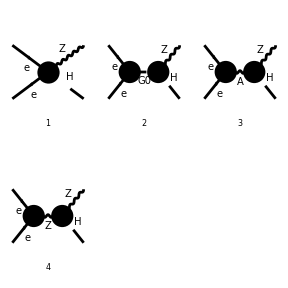

```mathematica
tops=CreateTopologies[0,2->2,Adjacencies->{3,4},ExcludeTopologies->{Tadpoles,WFCorrections}];
D1=InsertFields[tops,{F[4],-F[4]}->{V[2],S[1]},InsertionLevel->{Particles},ExcludeParticles->{},Model->$NBDIR<>"SMEFTatLO_MW_U2^2xU3^3_FA/SMEFTatLO_MW_U2^2xU3^3_FA",GenericModel->$NBDIR<>"SMEFTatLO_MW_U2^2xU3^3_FA/SMEFTatLO_MW_U2^2xU3^3_FA"];
Paint[D1, Numbering->Simple];
```

```mathematica
AmpFA=CreateFeynAmp[D1, Truncated->False]/.cF3ll->0/.cF3pl1->0/.cF3pl2->0/.{GS->FAGS,SUNT->FASUNT,SUNF->FASUNF,FeynAmp->FAFeynAmp,PropagatorDenominator->FAPropagatorDenominator,MetricTensor->FAMetricTensor,NonCommutative->FANonCommutative,DiracSpinor->FADiracSpinor,DiracMatrix->FADiracMatrix,PolarizationVector->FAPolarizationVector}/.GaugeXi[a_]:>1/.cw0^2+sw0^2->1;
AmpFA>>"/Users/user/Desktop/eeZH_AmpFA.dat";
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 3 Particles amplitudes

in total: 4 Particles amplitudes

```mathematica
Quit[]
```

```mathematica
AmpFA=Get["/Users/user/Desktop/eeZH_AmpFA.dat"];
AmpFC = FCFAConvert[AmpFA,IncomingMomenta->{p1, p2},OutgoingMomenta->{p3,p4},List->False,ChangeDimension->4,SMP->True,DropSumOver->False,UndoChiralSplittings->True]//Simplify//PropagatorDenominatorExplicit//Contract
```

1083+(cpl1 4 vev0)/(2 cw0 6^2 (s-MZ^2))+(c3pl1 cw0 ee0 (φ(-OverBar[p2])).(γ̄·(-OverBar[p3]-OverBar[p4])).(γ̄)^7.(φ(OverBar[p1])) (OverBar[p3]·(ε̄)^*(p3)+OverBar[p4]·(ε̄)^*(p3)) vev0)/(2 Lambda^2 (s-MZ^2) sw0)+(cpl1 cw0 ee0 (φ(-OverBar[p2])).(γ̄·(-OverBar[p3]-OverBar[p4])).(γ̄)^7.(φ(OverBar[p1])) (OverBar[p3]·(ε̄)^*(p3)+OverBar[p4]·(ε̄)^*(p3)) vev0)/(2 Lambda^2 (s-MZ^2) sw0)
 |  |  |  |

```mathematica
amp1=(AmpFC/.cw0^2+sw0^2->1/.MZ->SMP["m_Z"]/.ElectronPolarised//DiracSimplify)/.PositronPolarised//DiracSimplify;
AmpAll=amp1/.swsub/.inputsubs/.aEWsub//MomentumExpand;
AmpFCTrunc =ReplaceAll[AmpAll//Expand,Power[Lambda,a_Integer]:>0 /;a<-2]//Simplify (*Keep up to 1/Lambda^2*)
```

1/(√GF Lambda^2 s m_W √(1-m_W^2/m_Z^2) m_Z (m_Z^2-s))√(GF m_W^2-(GF m_W^4)/m_Z^2) (-8 cpBB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) m_W^4+8 cpW (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) m_W^4-8 cpBB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_W^4+8 cpW (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_W^4-8 cpBB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) m_W^4+8 cpW (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) m_W^4-8 cpBB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_W^4+8 cpW (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_W^4+8 cpWB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) √(1-m_W^2/m_Z^2) m_Z m_W^3+8 cpWB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) √(1-m_W^2/m_Z^2) m_Z m_W^3+8 cpWB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) √(1-m_W^2/m_Z^2) m_Z m_W^3+8 cpWB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) √(1-m_W^2/m_Z^2) m_Z m_W^3+8 cpBB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2 m_W^2-8 cpW (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2 m_W^2+8 cpBB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2 m_W^2-8 cpW (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2 m_W^2+8 cpBB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2 m_W^2-8 cpW (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2 m_W^2+8 cpBB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2 m_W^2-8 cpW (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2 m_W^2+8 cpBB s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) m_W^2+4 cpBB s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_W^2+4 cpW s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_W^2+8 cpBB s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) m_W^2+4 cpBB s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_W^2+4 cpW s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_W^2-4 cpWB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) √(1-m_W^2/m_Z^2) m_Z^3 m_W-4 cpWB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) √(1-m_W^2/m_Z^2) m_Z^3 m_W-4 cpWB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) √(1-m_W^2/m_Z^2) m_Z^3 m_W-4 cpWB (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) √(1-m_W^2/m_Z^2) m_Z^3 m_W-4 cpWB s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) √(1-m_W^2/m_Z^2) m_Z m_W-4 cpWB s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) √(1-m_W^2/m_Z^2) m_Z m_W-8 cpBB s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2+cpe s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2+cpe s (φ(-OverBar[p2])).(γ̄·OverBar[p4]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2+c3pl1 s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2-4 cpBB s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2+cpl1 s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2+c3pl1 s (φ(-OverBar[p2])).(γ̄·OverBar[p4]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2+cpl1 s (φ(-OverBar[p2])).(γ̄·OverBar[p4]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p3]·(ε̄)^*(p3)) m_Z^2-8 cpBB s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2+2 cpe s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2+2 cpe s (φ(-OverBar[p2])).(γ̄·OverBar[p4]).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2+2 c3pl1 s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2-4 cpBB s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2+2 cpl1 s (φ(-OverBar[p2])).(γ̄·OverBar[p3]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2+2 c3pl1 s (φ(-OverBar[p2])).(γ̄·OverBar[p4]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2+2 cpl1 s (φ(-OverBar[p2])).(γ̄·OverBar[p4]).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (OverBar[p4]·(ε̄)^*(p3)) m_Z^2-2 (φ(-OverBar[p2])).(γ̄·(ε̄)^*(p3)).(γ̄)^6.(φ(OverBar[p1])) √(fL(e+)) √(fR(e-)) (-2 (cpBB-cpW) (-m_H^2+m_Z^2+s) m_W^4+2 cpWB √(1-m_W^2/m_Z^2) m_Z (-m_H^2+m_Z^2+s) m_W^3+(2 (cpBB-cpW) m_Z^4+(2 √2 GF Lambda^2-2 c3pl1-2 c3pl2+2 cdp+2 cll1221+4 cpBB+cpDC-2 cpW) s m_Z^2+2 cpBB s^2-2 m_H^2 ((cpBB-cpW) m_Z^2+cpBB s)) m_W^2-cpWB √(1-m_W^2/m_Z^2) m_Z (m_Z^4+s^2-m_H^2 (m_Z^2+s)) m_W+s m_Z^2 (2 cpBB m_H^2+2 (-√2 GF Lambda^2+c3pl1+c3pl2-cdp-cll1221-cpBB) m_Z^2+(cpe-2 cpBB) s))-2 (φ(-OverBar[p2])).(γ̄·(ε̄)^*(p3)).(γ̄)^7.(φ(OverBar[p1])) √(fL(e-)) √(fR(e+)) (-2 (cpBB-cpW) (-m_H^2+m_Z^2+s) m_W^4+2 cpWB √(1-m_W^2/m_Z^2) m_Z (-m_H^2+m_Z^2+s) m_W^3+(2 (cpBB-cpW) m_Z^4+(2 √2 GF Lambda^2-2 c3pl1-2 c3pl2+2 cdp+2 cll1221+3 cpBB+cpDC-cpW) s m_Z^2+(cpBB+cpW) s^2-m_H^2 (2 (cpBB-cpW) m_Z^2+(cpBB+cpW) s)) m_W^2+cpWB √(1-m_W^2/m_Z^2) m_Z^3 (m_H^2-m_Z^2+s) m_W+s m_Z^2 (cpBB m_H^2+(-√2 GF Lambda^2+c3pl1+c3pl2-cdp-cll1221-cpBB) m_Z^2+(c3pl1-cpBB+cpl1) s)))

```mathematica
(*AmpFCTrunc>>"/Users/user/Desktop/eeZH_AmpFCTrunc.dat"*)
```

```mathematica
AmpFCTrunc=Get["/Users/user/Desktop/eeZH_AmpFCTrunc.dat"];
amp2=AmpFCTrunc*ComplexConjugate[AmpFCTrunc]//Simplify;
spinsum=(FermionSpinSum[amp2]//DiracSimplify)/.η->1//EchoTiming;
spinsum2=Collect2[spinsum,Eps]//EchoTiming;
spinsum3=Collect2[spinsum,Eps,Polarization]//EchoTiming;
spinsum4={};
Do[spinsum4=Append[spinsum4,DoPolarizationSums[spinsum3[[i]]/.η->1,p3]],{i,1,spinsum3//Length}]//EchoTiming;
amp2avg=(spinsum4/.{u->SMP["m_Z"]^2+SMP["m_H"]^2-s-t})//Total//Simplify//EchoTiming
```

5.3913

49.4548

23.1351

5.10181

38.0786

1/(Lambda^4 s m_Z^2 (s-m_Z^2)^2)(4 fL(e+) fR(e-) (8 (cpBB^2-2 cpW cpBB+cpW^2-cpWB^2) (m_H^4-2 (s+t) m_H^2+m_Z^4+s^2+2 t^2+2 (s-t) m_Z^2+2 s t) m_W^8-16 (cpBB-cpW) cpWB √(1-m_W^2/m_Z^2) m_Z (m_H^4-2 (s+t) m_H^2+m_Z^4+s^2+2 t^2+2 (s-t) m_Z^2+2 s t) m_W^7-8 (2 (cpBB^2-2 cpW cpBB+cpW^2-cpWB^2) m_Z^6+(6 s cpBB^2-4 t cpBB^2+2 √2 GF Lambda^2 s cpBB+2 cdp s cpBB+2 cll1221 s cpBB+cpDC s cpBB-10 cpW s cpBB+8 cpW t cpBB+4 cpW^2 s-3 cpWB^2 s-2 √2 cpW GF Lambda^2 s-2 cdp cpW s-2 cll1221 cpW s-cpDC cpW s+2 c3pl1 (cpW-cpBB) s+2 c3pl2 (cpW-cpBB) s-4 cpW^2 t+4 cpWB^2 t) m_Z^4+(2 s^2 cpW^2+4 t^2 cpW^2+4 s t cpW^2-2 √2 GF Lambda^2 s^2 cpW-2 cdp s^2 cpW-2 cll1221 s^2 cpW-8 cpBB s^2 cpW-cpDC s^2 cpW-8 cpBB t^2 cpW-4 cpBB s t cpW+6 cpBB^2 s^2-2 cpWB^2 s^2+2 √2 cpBB GF Lambda^2 s^2+2 cdp cpBB s^2+2 cll1221 cpBB s^2+cpBB cpDC s^2+2 c3pl1 (cpW-cpBB) s^2+2 c3pl2 (cpW-cpBB) s^2+4 cpBB^2 t^2-4 cpWB^2 t^2-2 cpWB^2 s t) m_Z^2+(2 cpBB^2-2 cpW cpBB-cpWB^2) s (s^2+2 t s+2 t^2)+m_H^4 (2 (cpBB^2-2 cpW cpBB+cpW^2-cpWB^2) m_Z^2+(2 cpBB^2-2 cpW cpBB-cpWB^2) s)+m_H^2 ((-4 s cpBB^2-4 t cpBB^2-2 √2 GF Lambda^2 s cpBB-2 cdp s cpBB-2 cll1221 s cpBB-cpDC s cpBB+8 cpW s cpBB+8 cpW t cpBB-4 cpW^2 s+2 cpWB^2 s+2 √2 cpW GF Lambda^2 s+2 c3pl1 (cpBB-cpW) s+2 c3pl2 (cpBB-cpW) s+2 cdp cpW s+2 cll1221 cpW s+cpDC cpW s-4 cpW^2 t+4 cpWB^2 t) m_Z^2-2 (2 cpBB^2-2 cpW cpBB-cpWB^2) s (s+t))) m_W^6+8 cpWB √(1-m_W^2/m_Z^2) m_Z (3 (cpBB-cpW) m_Z^6+(2 √2 GF s Lambda^2-2 c3pl1 s-2 c3pl2 s+2 cdp s+2 cll1221 s+7 cpBB s+cpDC s-5 cpW s-6 cpBB t+6 cpW t) m_Z^4+(2 √2 GF Lambda^2 s^2-2 c3pl1 s^2-2 c3pl2 s^2+2 cdp s^2+2 cll1221 s^2+7 cpBB s^2+cpDC s^2-3 cpW s^2-4 cpW t s+6 cpBB t^2-6 cpW t^2) m_Z^2+(3 cpBB-cpW) s (s^2+2 t s+2 t^2)+m_H^4 (3 (cpBB-cpW) m_Z^2+(3 cpBB-cpW) s)-m_H^2 ((2 √2 GF s Lambda^2-2 c3pl1 s-2 c3pl2 s+2 cdp s+2 cll1221 s+4 cpBB s+cpDC s-4 cpW s+6 cpBB t-6 cpW t) m_Z^2+2 (3 cpBB-cpW) s (s+t))) m_W^5+(2 (4 cpBB^2-8 cpW cpBB+4 cpW^2-5 cpWB^2) m_Z^8-4 (-12 s cpBB^2+4 t cpBB^2-8 √2 GF Lambda^2 s cpBB-8 cdp s cpBB-8 cll1221 s cpBB-2 cpDC s cpBB+16 cpW s cpBB-8 cpW t cpBB-4 cpW^2 s+2 cpWB^2 s+8 √2 cpW GF Lambda^2 s+8 c3pl1 (cpBB-cpW) s+8 c3pl2 (cpBB-cpW) s+8 cdp cpW s+8 cll1221 cpW s+2 cpDC cpW s+4 cpW^2 t-5 cpWB^2 t) m_Z^6+(16 GF^2 s^2 Lambda^4+8 GF^2 s t Lambda^4+16 √2 cdp GF s^2 Lambda^2+16 √2 cll1221 GF s^2 Lambda^2+48 √2 cpBB GF s^2 Lambda^2+8 √2 cpDC GF s^2 Lambda^2-32 √2 cpW GF s^2 Lambda^2+8 √2 cdp GF s t Lambda^2+8 √2 cll1221 GF s t Lambda^2+4 √2 cpDC GF s t Lambda^2+8 cdp^2 s^2+8 cll1221^2 s^2+80 cpBB^2 s^2+2 cpDC^2 s^2+8 cpW^2 s^2-12 cpWB^2 s^2+16 cdp cll1221 s^2+48 cdp cpBB s^2+48 cll1221 cpBB s^2+8 cdp cpDC s^2+8 cll1221 cpDC s^2+16 cpBB cpDC s^2-8 cpBB cpe s^2-32 cdp cpW s^2-32 cll1221 cpW s^2-80 cpBB cpW s^2-8 cpDC cpW s^2+8 cpe cpW s^2+16 cpBB^2 t^2+16 cpW^2 t^2-20 cpWB^2 t^2-32 cpBB cpW t^2+4 cdp^2 s t+4 cll1221^2 s t-48 cpBB^2 s t+cpDC^2 s t+16 cpW^2 s t+8 cdp cll1221 s t+4 cdp cpDC s t+4 cll1221 cpDC s t+32 cpBB cpW s t+4 c3pl1^2 s (2 s+t)+4 c3pl2^2 s (2 s+t)-4 c3pl2 s (4 √2 GF s Lambda^2+2 √2 GF t Lambda^2+4 cdp s+4 cll1221 s+12 cpBB s+2 cpDC s-8 cpW s+2 cdp t+2 cll1221 t+cpDC t)-4 c3pl1 s (4 √2 GF s Lambda^2+2 √2 GF t Lambda^2+4 cdp s+4 cll1221 s+12 cpBB s+2 cpDC s-8 cpW s+2 cdp t+2 cll1221 t+cpDC t-2 c3pl2 (2 s+t))) m_Z^4-s (8 GF^2 t^2 Lambda^4+8 GF^2 s t Lambda^4-16 √2 cpBB GF s^2 Lambda^2+8 √2 cdp GF t^2 Lambda^2+8 √2 cll1221 GF t^2 Lambda^2+4 √2 cpDC GF t^2 Lambda^2+8 √2 cdp GF s t Lambda^2+8 √2 cll1221 GF s t Lambda^2+4 √2 cpDC GF s t Lambda^2-48 cpBB^2 s^2+8 cpWB^2 s^2+16 c3pl2 cpBB s^2-16 cdp cpBB s^2-16 cll1221 cpBB s^2-8 cpBB cpDC s^2+8 cpBB cpe s^2+32 cpBB cpW s^2-8 cpe cpW s^2+4 cdp^2 t^2+4 cll1221^2 t^2-64 cpBB^2 t^2+cpDC^2 t^2+20 cpWB^2 t^2+8 cdp cll1221 t^2+4 cdp cpDC t^2+4 cll1221 cpDC t^2+64 cpBB cpW t^2+4 cdp^2 s t+4 cll1221^2 s t-48 cpBB^2 s t+cpDC^2 s t+16 cpWB^2 s t+8 cdp cll1221 s t+4 cdp cpDC s t+4 cll1221 cpDC s t+64 cpBB cpW s t+4 c3pl1^2 t (s+t)+4 c3pl2^2 t (s+t)-4 c3pl2 (2 √2 GF Lambda^2+2 cdp+2 cll1221+cpDC) t (s+t)+4 c3pl1 (4 cpBB s^2+(-2 √2 GF Lambda^2+2 c3pl2-2 cdp-2 cll1221-cpDC) t (s+t))) m_Z^2+2 (4 cpBB^2-cpWB^2) s^2 (s^2+2 t s+2 t^2)+2 m_H^4 ((4 cpBB^2-8 cpW cpBB+4 cpW^2-5 cpWB^2) m_Z^4+2 (8 cpBB^2-8 cpW cpBB-3 cpWB^2) s m_Z^2+(4 cpBB^2-cpWB^2) s^2)+m_H^2 (-((8 GF^2 s Lambda^4+8 √2 cdp GF s Lambda^2+8 √2 cll1221 GF s Lambda^2+32 √2 cpBB GF s Lambda^2+4 √2 cpDC GF s Lambda^2-32 √2 cpW GF s Lambda^2+4 c3pl1^2 s+4 c3pl2^2 s+4 cdp^2 s+4 cll1221^2 s+16 cpBB^2 s+cpDC^2 s+16 cpW^2 s+8 cdp cll1221 s+32 cdp cpBB s+32 cll1221 cpBB s+4 cdp cpDC s+4 cll1221 cpDC s+8 cpBB cpDC s-32 cdp cpW s-32 cll1221 cpW s-32 cpBB cpW s-8 cpDC cpW s+4 c3pl1 (-2 √2 GF Lambda^2+2 c3pl2-2 cdp-2 cll1221-8 cpBB-cpDC+8 cpW) s-4 c3pl2 (2 √2 GF Lambda^2+2 cdp+2 cll1221+8 cpBB+cpDC-8 cpW) s+16 cpBB^2 t+16 cpW^2 t-20 cpWB^2 t-32 cpBB cpW t) m_Z^4)+s (8 GF^2 t Lambda^4-16 √2 cpBB GF s Lambda^2+8 √2 cdp GF t Lambda^2+8 √2 cll1221 GF t Lambda^2+4 √2 cpDC GF t Lambda^2-64 cpBB^2 s+16 cpWB^2 s+16 c3pl2 cpBB s-16 cdp cpBB s-16 cll1221 cpBB s-8 cpBB cpDC s+8 cpBB cpe s+64 cpBB cpW s-8 cpe cpW s+4 c3pl1^2 t+4 c3pl2^2 t+4 cdp^2 t+4 cll1221^2 t-64 cpBB^2 t+cpDC^2 t+20 cpWB^2 t+8 cdp cll1221 t+4 cdp cpDC t+4 cll1221 cpDC t+64 cpBB cpW t-4 c3pl2 (2 √2 GF Lambda^2+2 cdp+2 cll1221+cpDC) t+4 c3pl1 (4 cpBB s+(-2 √2 GF Lambda^2+2 c3pl2-2 cdp-2 cll1221-cpDC) t)) m_Z^2-4 (4 cpBB^2-cpWB^2) s^2 (s+t))) m_W^4-4 cpWB √(1-m_W^2/m_Z^2) m_Z (2 (cpBB-cpW) m_Z^8+(6 √2 GF s Lambda^2-6 c3pl1 s-6 c3pl2 s+6 cdp s+6 cll1221 s+8 cpBB s+cpDC s-2 cpW s-4 cpBB t+4 cpW t) m_Z^6-(-4 √2 GF s^2 Lambda^2+2 √2 GF s t Lambda^2-4 cdp s^2-4 cll1221 s^2-12 cpBB s^2+2 cpe s^2+2 cpW s^2-4 cpBB t^2+4 cpW t^2+2 c3pl1 s (2 s-t)+2 c3pl2 s (2 s-t)+2 cdp s t+2 cll1221 s t+12 cpBB s t+cpDC s t) m_Z^4+s (2 √2 GF s^2 Lambda^2+2 √2 GF t^2 Lambda^2+2 √2 GF s t Lambda^2+2 cdp s^2+2 cll1221 s^2+8 cpBB s^2+cpDC s^2-2 cpe s^2-2 cpW s^2+2 cdp t^2+2 cll1221 t^2+16 cpBB t^2+cpDC t^2-4 cpW t^2+2 cdp s t+2 cll1221 s t+12 cpBB s t+cpDC s t-4 cpW s t-2 c3pl1 (s^2+t s+t^2)-2 c3pl2 (s^2+t s+t^2)) m_Z^2+2 cpBB s^2 (s^2+2 t s+2 t^2)+2 m_H^4 ((cpBB-cpW) m_Z^4+(4 cpBB-cpW) s m_Z^2+cpBB s^2)-m_H^2 (-4 (-√2 GF s Lambda^2+c3pl1 s+c3pl2 s-cdp s-cll1221 s-cpBB t+cpW t) m_Z^4+s (2 √2 GF s Lambda^2+2 √2 GF t Lambda^2+2 cdp s+2 cll1221 s+12 cpBB s+cpDC s-2 cpe s-4 cpW s+2 cdp t+2 cll1221 t+16 cpBB t+cpDC t-4 cpW t-2 c3pl1 (s+t)-2 c3pl2 (s+t)) m_Z^2+4 cpBB s^2 (s+t))) m_W^3+2 m_Z^2 (cpWB^2 m_Z^8+(-8 s cpBB^2-8 √2 GF Lambda^2 s cpBB-8 cdp s cpBB-8 cll1221 s cpBB+8 cpW s cpBB+8 √2 cpW GF Lambda^2 s+8 c3pl1 (cpBB-cpW) s+8 c3pl2 (cpBB-cpW) s+8 cdp cpW s+8 cll1221 cpW s-2 cpWB^2 t) m_Z^6-2 (8 GF^2 s^2 Lambda^4+4 GF^2 s t Lambda^4+8 √2 cdp GF s^2 Lambda^2+8 √2 cll1221 GF s^2 Lambda^2+12 √2 cpBB GF s^2 Lambda^2+2 √2 cpDC GF s^2 Lambda^2-4 √2 cpW GF s^2 Lambda^2+4 √2 cdp GF s t Lambda^2+4 √2 cll1221 GF s t Lambda^2+√2 cpDC GF s t Lambda^2+4 cdp^2 s^2+4 cll1221^2 s^2+12 cpBB^2 s^2-cpWB^2 s^2+8 cdp cll1221 s^2+12 cdp cpBB s^2+12 cll1221 cpBB s^2+2 cdp cpDC s^2+2 cll1221 cpDC s^2+2 cpBB cpDC s^2-2 cpBB cpe s^2-4 cdp cpW s^2-4 cll1221 cpW s^2-8 cpBB cpW s^2+2 cpe cpW s^2-cpWB^2 t^2+2 cdp^2 s t+2 cll1221^2 s t-8 cpBB^2 s t+4 cdp cll1221 s t+cdp cpDC s t+cll1221 cpDC s t+8 cpBB cpW s t+2 c3pl1^2 s (2 s+t)+2 c3pl2^2 s (2 s+t)-c3pl2 s (8 √2 GF s Lambda^2+4 √2 GF t Lambda^2+8 cdp s+8 cll1221 s+12 cpBB s+2 cpDC s-4 cpW s+4 cdp t+4 cll1221 t+cpDC t)-c3pl1 s (8 √2 GF s Lambda^2+4 √2 GF t Lambda^2+8 cdp s+8 cll1221 s+12 cpBB s+2 cpDC s-4 cpW s+4 cdp t+4 cll1221 t+cpDC t-4 c3pl2 (2 s+t))) m_Z^4+s (8 GF^2 t^2 Lambda^4+8 GF^2 s t Lambda^4-16 √2 cpBB GF s^2 Lambda^2+4 √2 cpe GF s^2 Lambda^2-8 √2 c3pl2 GF t^2 Lambda^2+8 √2 cdp GF t^2 Lambda^2+8 √2 cll1221 GF t^2 Lambda^2+2 √2 cpDC GF t^2 Lambda^2-8 √2 c3pl2 GF s t Lambda^2+8 √2 cdp GF s t Lambda^2+8 √2 cll1221 GF s t Lambda^2+2 √2 cpDC GF s t Lambda^2+2 √2 cpe GF s t Lambda^2-24 cpBB^2 s^2+16 c3pl2 cpBB s^2-16 cdp cpBB s^2-16 cll1221 cpBB s^2-4 cpBB cpDC s^2-4 c3pl2 cpe s^2+4 cdp cpe s^2+4 cll1221 cpe s^2+8 cpBB cpe s^2+2 cpDC cpe s^2+8 cpBB cpW s^2-4 cpe cpW s^2+4 c3pl2^2 t^2+4 cdp^2 t^2+4 cll1221^2 t^2-16 cpBB^2 t^2+2 cpWB^2 t^2-8 c3pl2 cdp t^2-8 c3pl2 cll1221 t^2+8 cdp cll1221 t^2-2 c3pl2 cpDC t^2+2 cdp cpDC t^2+2 cll1221 cpDC t^2+16 cpBB cpW t^2+4 c3pl2^2 s t+4 cdp^2 s t+4 cll1221^2 s t-8 c3pl2 cdp s t-8 c3pl2 cll1221 s t+8 cdp cll1221 s t-2 c3pl2 cpDC s t+2 cdp cpDC s t+2 cll1221 cpDC s t-2 c3pl2 cpe s t+2 cdp cpe s t+2 cll1221 cpe s t+cpDC cpe s t+16 cpBB cpW s t+4 c3pl1^2 t (s+t)+2 c3pl1 (8 cpBB s^2-cpe (2 s+t) s+(-4 √2 GF Lambda^2+4 c3pl2-4 cdp-4 cll1221-cpDC) t (s+t))) m_Z^2+s^2 (-8 (s^2+2 t s+2 t^2) cpBB^2+4 cpe s^2 cpBB+cpe (-2 √2 GF Lambda^2+2 c3pl1+2 c3pl2-2 cdp-2 cll1221-cpDC) t (s+t)+cpWB^2 (s^2+2 t s+2 t^2))+m_H^4 (cpWB^2 m_Z^4+2 (-4 cpBB^2+4 cpW cpBB+cpWB^2) s m_Z^2+(cpWB^2-8 cpBB^2) s^2)+m_H^2 (2 (4 GF^2 s Lambda^4+4 √2 cdp GF s Lambda^2+4 √2 cll1221 GF s Lambda^2+4 √2 cpBB GF s Lambda^2+√2 cpDC GF s Lambda^2-4 √2 cpW GF s Lambda^2+2 c3pl1^2 s+2 c3pl2^2 s+2 cdp^2 s+2 cll1221^2 s+4 cdp cll1221 s+4 cdp cpBB s+4 cll1221 cpBB s+cdp cpDC s+cll1221 cpDC s-4 cdp cpW s-4 cll1221 cpW s+c3pl1 (-4 √2 GF Lambda^2+4 c3pl2-4 cdp-4 cll1221-4 cpBB-cpDC+4 cpW) s-c3pl2 (4 √2 GF Lambda^2+4 cdp+4 cll1221+4 cpBB+cpDC-4 cpW) s-cpWB^2 t) m_Z^4-s (8 GF^2 t Lambda^4-16 √2 cpBB GF s Lambda^2+2 √2 cpe GF s Lambda^2+8 √2 cdp GF t Lambda^2+8 √2 cll1221 GF t Lambda^2+2 √2 cpDC GF t Lambda^2-16 cpBB^2 s-16 cdp cpBB s-16 cll1221 cpBB s-4 cpBB cpDC s+2 cdp cpe s+2 cll1221 cpe s+4 cpBB cpe s+cpDC cpe s+16 cpBB cpW s-4 cpe cpW s+4 c3pl1^2 t+4 c3pl2^2 t+4 cdp^2 t+4 cll1221^2 t-16 cpBB^2 t+2 cpWB^2 t+8 cdp cll1221 t+2 cdp cpDC t+2 cll1221 cpDC t+16 cpBB cpW t+2 c3pl1 (8 cpBB s-cpe s+(-4 √2 GF Lambda^2+4 c3pl2-4 cdp-4 cll1221-cpDC) t)+2 c3pl2 (8 cpBB s-cpe s-(4 √2 GF Lambda^2+4 cdp+4 cll1221+cpDC) t)) m_Z^2+s^2 (16 (s+t) cpBB^2-4 cpe s cpBB+cpe (2 √2 GF Lambda^2-2 c3pl1-2 c3pl2+2 cdp+2 cll1221+cpDC) t-2 cpWB^2 (s+t)))) m_W^2+4 cpWB s √(1-m_W^2/m_Z^2) m_Z^3 (-2 (-√2 GF Lambda^2+c3pl1+c3pl2-cdp-cll1221-cpBB) m_Z^6-(cpe s-2 cpBB (s-2 t)+2 (√2 GF Lambda^2-c3pl1-c3pl2+cdp+cll1221) t) m_Z^4+(2 √2 GF s^2 Lambda^2+2 √2 GF t^2 Lambda^2+2 √2 GF s t Lambda^2+2 cdp s^2+2 cll1221 s^2+2 cpBB s^2+2 cdp t^2+2 cll1221 t^2+4 cpBB t^2+2 cdp s t+2 cll1221 s t+cpe s t-2 c3pl1 (s^2+t s+t^2)-2 c3pl2 (s^2+t s+t^2)) m_Z^2+s (2 cpBB (s^2+2 t s+2 t^2)-cpe (s^2+t s+t^2))+2 cpBB m_H^4 (m_Z^2+s)+m_H^2 (-2 (√2 GF s Lambda^2+√2 GF t Lambda^2+cdp s+cll1221 s+cdp t+cll1221 t+2 cpBB t-c3pl1 (s+t)-c3pl2 (s+t)) m_Z^2-(4 cpBB-cpe) s (s+t))) m_W+s m_Z^2 (4 (4 GF^2 s Lambda^4+2 GF^2 t Lambda^4+4 √2 cdp GF s Lambda^2+4 √2 cll1221 GF s Lambda^2+4 √2 cpBB GF s Lambda^2+2 √2 cdp GF t Lambda^2+2 √2 cll1221 GF t Lambda^2+2 cdp^2 s+2 cll1221^2 s+2 cpBB^2 s+4 cdp cll1221 s+4 cdp cpBB s+4 cll1221 cpBB s+cdp^2 t+cll1221^2 t+2 cdp cll1221 t+c3pl1^2 (2 s+t)+c3pl2^2 (2 s+t)-2 c3pl2 (2 √2 GF s Lambda^2+√2 GF t Lambda^2+2 cdp s+2 cll1221 s+2 cpBB s+cdp t+cll1221 t)-2 c3pl1 (2 √2 GF s Lambda^2+√2 GF t Lambda^2+2 cdp s+2 cll1221 s+2 cpBB s+cdp t+cll1221 t-c3pl2 (2 s+t))) m_Z^6-4 (2 GF^2 t^2 Lambda^4+2 GF^2 s t Lambda^4-4 √2 cpBB GF s^2 Lambda^2+2 √2 cpe GF s^2 Lambda^2-2 √2 c3pl2 GF t^2 Lambda^2+2 √2 cdp GF t^2 Lambda^2+2 √2 cll1221 GF t^2 Lambda^2-2 √2 c3pl2 GF s t Lambda^2+2 √2 cdp GF s t Lambda^2+2 √2 cll1221 GF s t Lambda^2+√2 cpe GF s t Lambda^2-4 cpBB^2 s^2+4 c3pl2 cpBB s^2-4 cdp cpBB s^2-4 cll1221 cpBB s^2-2 c3pl2 cpe s^2+2 cdp cpe s^2+2 cll1221 cpe s^2+2 cpBB cpe s^2+c3pl2^2 t^2+cdp^2 t^2+cll1221^2 t^2-2 c3pl2 cdp t^2-2 c3pl2 cll1221 t^2+2 cdp cll1221 t^2+c3pl2^2 s t+cdp^2 s t+cll1221^2 s t+4 cpBB^2 s t-2 c3pl2 cdp s t-2 c3pl2 cll1221 s t+2 cdp cll1221 s t-c3pl2 cpe s t+cdp cpe s t+cll1221 cpe s t+c3pl1^2 t (s+t)+c3pl1 (4 cpBB s^2-cpe (2 s+t) s+2 (-√2 GF Lambda^2+c3pl2-cdp-cll1221) t (s+t))) m_Z^4+8 cpBB^2 s m_H^4 m_Z^2+s (8 (s^2+2 t s+2 t^2) cpBB^2-8 cpe s^2 cpBB+cpe (cpe s (2 s+t)-4 (-√2 GF Lambda^2+c3pl1+c3pl2-cdp-cll1221) t (s+t))) m_Z^2-cpe^2 s^2 t (s+t)+m_H^2 (-4 (2 GF^2 Lambda^4+2 √2 cdp GF Lambda^2+2 √2 cll1221 GF Lambda^2+c3pl1^2+c3pl2^2+cdp^2+cll1221^2+2 cdp cll1221+2 c3pl1 (-√2 GF Lambda^2+c3pl2-cdp-cll1221)-2 c3pl2 (√2 GF Lambda^2+cdp+cll1221)) m_Z^6+4 (2 GF^2 t Lambda^4-4 √2 cpBB GF s Lambda^2+√2 cpe GF s Lambda^2+2 √2 cdp GF t Lambda^2+2 √2 cll1221 GF t Lambda^2-4 cdp cpBB s-4 cll1221 cpBB s+cdp cpe s+cll1221 cpe s+c3pl1^2 t+c3pl2^2 t+cdp^2 t+cll1221^2 t+2 cdp cll1221 t+c3pl1 (4 cpBB s-cpe s+2 (-√2 GF Lambda^2+c3pl2-cdp-cll1221) t)+c3pl2 (4 cpBB s-cpe s-2 (√2 GF Lambda^2+cdp+cll1221) t)) m_Z^4-s (16 (s+t) cpBB^2-8 cpe s cpBB+cpe (cpe s+4 (√2 GF Lambda^2-c3pl1-c3pl2+cdp+cll1221) t)) m_Z^2+cpe^2 s^2 t)))+4 fL(e-) fR(e+) (8 (cpBB^2-2 cpW cpBB+cpW^2-cpWB^2) (m_H^4-2 (s+t) m_H^2+m_Z^4+s^2+2 t^2+2 (s-t) m_Z^2+2 s t) m_W^8-16 (cpBB-cpW) cpWB √(1-m_W^2/m_Z^2) m_Z (m_H^4-2 (s+t) m_H^2+m_Z^4+s^2+2 t^2+2 (s-t) m_Z^2+2 s t) m_W^7-8 (2 (cpBB^2-2 cpW cpBB+cpW^2-cpWB^2) m_Z^6+(5 s cpBB^2-4 t cpBB^2+2 √2 GF Lambda^2 s cpBB+2 cdp s cpBB+2 cll1221 s cpBB+cpDC s cpBB-8 cpW s cpBB+8 cpW t cpBB+3 cpW^2 s-2 cpWB^2 s-2 √2 cpW GF Lambda^2 s-2 cdp cpW s-2 cll1221 cpW s-cpDC cpW s+2 c3pl1 (cpW-cpBB) s+2 c3pl2 (cpW-cpBB) s-4 cpW^2 t+4 cpWB^2 t) m_Z^4+(4 s^2 cpBB^2+4 t^2 cpBB^2+2 s t cpBB^2+2 √2 GF Lambda^2 s^2 cpBB+2 cdp s^2 cpBB+2 cll1221 s^2 cpBB+cpDC s^2 cpBB-4 cpW s^2 cpBB-8 cpW t^2 cpBB-8 cpW s t cpBB-2 √2 cpW GF Lambda^2 s^2-2 cdp cpW s^2-2 cll1221 cpW s^2-cpDC cpW s^2+2 c3pl1 (cpW-cpBB) s^2+2 c3pl2 (cpW-cpBB) s^2+4 cpW^2 t^2-4 cpWB^2 t^2+6 cpW^2 s t-4 cpWB^2 s t) m_Z^2+(cpBB^2-cpW^2) s (s^2+2 t s+2 t^2)+m_H^4 (2 (cpBB^2-2 cpW cpBB+cpW^2-cpWB^2) m_Z^2+(cpBB^2-cpW^2) s)+m_H^2 ((-4 s cpBB^2-4 t cpBB^2-2 √2 GF Lambda^2 s cpBB-2 cdp s cpBB-2 cll1221 s cpBB-cpDC s cpBB+8 cpW s cpBB+8 cpW t cpBB-4 cpW^2 s+2 cpWB^2 s+2 √2 cpW GF Lambda^2 s+2 c3pl1 (cpBB-cpW) s+2 c3pl2 (cpBB-cpW) s+2 cdp cpW s+2 cll1221 cpW s+cpDC cpW s-4 cpW^2 t+4 cpWB^2 t) m_Z^2-2 (cpBB^2-cpW^2) s (s+t))) m_W^6+8 cpWB √(1-m_W^2/m_Z^2) m_Z (3 (cpBB-cpW) m_Z^6+(2 √2 GF s Lambda^2-2 c3pl1 s-2 c3pl2 s+2 cdp s+2 cll1221 s+5 cpBB s+cpDC s-3 cpW s-6 cpBB t+6 cpW t) m_Z^4+(2 √2 GF Lambda^2 s^2-2 c3pl1 s^2-2 c3pl2 s^2+2 cdp s^2+2 cll1221 s^2+3 cpBB s^2+cpDC s^2+cpW s^2+4 cpBB t s-8 cpW t s+6 cpBB t^2-6 cpW t^2) m_Z^2+(cpBB+cpW) s (s^2+2 t s+2 t^2)+m_H^4 (3 (cpBB-cpW) m_Z^2+(cpBB+cpW) s)-m_H^2 ((2 √2 GF s Lambda^2-2 c3pl1 s-2 c3pl2 s+2 cdp s+2 cll1221 s+4 cpBB s+cpDC s-4 cpW s+6 cpBB t-6 cpW t) m_Z^2+2 (cpBB+cpW) s (s+t))) m_W^5+(2 (4 cpBB^2-8 cpW cpBB+4 cpW^2-5 cpWB^2) m_Z^8+4 (8 s cpBB^2-4 t cpBB^2+6 √2 GF Lambda^2 s cpBB+6 cdp s cpBB+6 cll1221 s cpBB+2 cpDC s cpBB-10 cpW s cpBB+8 cpW t cpBB+2 cpW^2 s+cpWB^2 s-6 √2 cpW GF Lambda^2 s-6 cdp cpW s-6 cll1221 cpW s-2 cpDC cpW s+6 c3pl1 (cpW-cpBB) s+6 c3pl2 (cpW-cpBB) s-4 cpW^2 t+5 cpWB^2 t) m_Z^6+(16 GF^2 s^2 Lambda^4+8 GF^2 s t Lambda^4+16 √2 cdp GF s^2 Lambda^2+16 √2 cll1221 GF s^2 Lambda^2+32 √2 cpBB GF s^2 Lambda^2+8 √2 cpDC GF s^2 Lambda^2-16 √2 cpW GF s^2 Lambda^2+8 √2 cdp GF s t Lambda^2+8 √2 cll1221 GF s t Lambda^2+4 √2 cpDC GF s t Lambda^2+8 cdp^2 s^2+8 cll1221^2 s^2+42 cpBB^2 s^2+2 cpDC^2 s^2-6 cpW^2 s^2+6 cpWB^2 s^2+16 cdp cll1221 s^2+32 cdp cpBB s^2+32 cll1221 cpBB s^2+8 cdp cpDC s^2+8 cll1221 cpDC s^2+12 cpBB cpDC s^2-8 cpBB cpl1 s^2-16 cdp cpW s^2-16 cll1221 cpW s^2-28 cpBB cpW s^2-4 cpDC cpW s^2+8 cpl1 cpW s^2+16 cpBB^2 t^2+16 cpW^2 t^2-20 cpWB^2 t^2-32 cpBB cpW t^2+4 cdp^2 s t+4 cll1221^2 s t-16 cpBB^2 s t+cpDC^2 s t+32 cpW^2 s t-24 cpWB^2 s t+8 cdp cll1221 s t+4 cdp cpDC s t+4 cll1221 cpDC s t-16 cpBB cpW s t+4 c3pl1^2 s (2 s+t)+4 c3pl2^2 s (2 s+t)-4 c3pl2 s (4 √2 GF s Lambda^2+2 √2 GF t Lambda^2+4 cdp s+4 cll1221 s+8 cpBB s+2 cpDC s-4 cpW s+2 cdp t+2 cll1221 t+cpDC t)-4 c3pl1 s (4 √2 GF s Lambda^2+2 √2 GF t Lambda^2+4 cdp s+4 cll1221 s+10 cpBB s+2 cpDC s-6 cpW s+2 cdp t+2 cll1221 t+cpDC t-2 c3pl2 (2 s+t))) m_Z^4-s (8 GF^2 t^2 Lambda^4+8 GF^2 s t Lambda^4-8 √2 cpBB GF s^2 Lambda^2-8 √2 cpW GF s^2 Lambda^2+8 √2 cdp GF t^2 Lambda^2+8 √2 cll1221 GF t^2 Lambda^2+4 √2 cpDC GF t^2 Lambda^2+8 √2 cdp GF s t Lambda^2+8 √2 cll1221 GF s t Lambda^2+4 √2 cpDC GF s t Lambda^2-20 cpBB^2 s^2+4 cpW^2 s^2-8 cdp cpBB s^2-8 cll1221 cpBB s^2-4 cpBB cpDC s^2+8 cpBB cpl1 s^2-8 cdp cpW s^2-8 cll1221 cpW s^2-4 cpDC cpW s^2-8 cpl1 cpW s^2+4 cdp^2 t^2+4 cll1221^2 t^2-32 cpBB^2 t^2+cpDC^2 t^2+16 cpW^2 t^2-4 cpWB^2 t^2+8 cdp cll1221 t^2+4 cdp cpDC t^2+4 cll1221 cpDC t^2+16 cpBB cpW t^2+4 cdp^2 s t+4 cll1221^2 s t-28 cpBB^2 s t+cpDC^2 s t+20 cpW^2 s t-4 cpWB^2 s t+8 cdp cll1221 s t+4 cdp cpDC s t+4 cll1221 cpDC s t+24 cpBB cpW s t+4 c3pl1^2 t (s+t)+4 c3pl2^2 t (s+t)+4 c3pl1 (4 cpBB s^2+(-2 √2 GF Lambda^2+2 c3pl2-2 cdp-2 cll1221-cpDC) t (s+t))+c3pl2 (8 cpBB s^2+8 cpW s^2-4 (2 √2 GF Lambda^2+2 cdp+2 cll1221+cpDC) t (s+t))) m_Z^2+2 (cpBB+cpW)^2 s^2 (s^2+2 t s+2 t^2)+2 m_H^4 ((4 cpBB^2-8 cpW cpBB+4 cpW^2-5 cpWB^2) m_Z^4+4 (2 cpBB^2-cpW cpBB-cpW^2) s m_Z^2+(cpBB+cpW)^2 s^2)-m_H^2 ((8 GF^2 s Lambda^4+8 √2 cdp GF s Lambda^2+8 √2 cll1221 GF s Lambda^2+24 √2 cpBB GF s Lambda^2+4 √2 cpDC GF s Lambda^2-24 √2 cpW GF s Lambda^2+4 c3pl1^2 s+4 c3pl2^2 s+4 cdp^2 s+4 cll1221^2 s+16 cpBB^2 s+cpDC^2 s+16 cpW^2 s+8 cdp cll1221 s+24 cdp cpBB s+24 cll1221 cpBB s+4 cdp cpDC s+4 cll1221 cpDC s+8 cpBB cpDC s-24 cdp cpW s-24 cll1221 cpW s-32 cpBB cpW s-8 cpDC cpW s+4 c3pl1 (-2 √2 GF Lambda^2+2 c3pl2-2 cdp-2 cll1221-6 cpBB-cpDC+6 cpW) s-4 c3pl2 (2 √2 GF Lambda^2+2 cdp+2 cll1221+6 cpBB+cpDC-6 cpW) s+16 cpBB^2 t+16 cpW^2 t-20 cpWB^2 t-32 cpBB cpW t) m_Z^4-s (8 GF^2 t Lambda^4-8 √2 cpBB GF s Lambda^2-8 √2 cpW GF s Lambda^2+8 √2 cdp GF t Lambda^2+8 √2 cll1221 GF t Lambda^2+4 √2 cpDC GF t Lambda^2-32 cpBB^2 s+16 cpW^2 s-8 cdp cpBB s-8 cll1221 cpBB s-4 cpBB cpDC s+8 cpBB cpl1 s-8 cdp cpW s-8 cll1221 cpW s+16 cpBB cpW s-4 cpDC cpW s-8 cpl1 cpW s+4 c3pl1^2 t+4 c3pl2^2 t+4 cdp^2 t+4 cll1221^2 t-32 cpBB^2 t+cpDC^2 t+16 cpW^2 t-4 cpWB^2 t+8 cdp cll1221 t+4 cdp cpDC t+4 cll1221 cpDC t+16 cpBB cpW t+4 c3pl1 (4 cpBB s+(-2 √2 GF Lambda^2+2 c3pl2-2 cdp-2 cll1221-cpDC) t)+c3pl2 (8 cpBB s+8 cpW s-4 (2 √2 GF Lambda^2+2 cdp+2 cll1221+cpDC) t)) m_Z^2+4 (cpBB+cpW)^2 s^2 (s+t))) m_W^4-4 cpWB √(1-m_W^2/m_Z^2) m_Z^3 (2 (cpBB-cpW) m_Z^6+(4 √2 GF s Lambda^2-4 c3pl1 s-4 c3pl2 s+4 cdp s+4 cll1221 s+3 cpBB s+cpDC s+cpW s-4 cpBB t+4 cpW t) m_Z^4-(2 √2 GF s t Lambda^2+cpDC s^2+2 cpl1 s^2-2 cpW s^2+4 cpW t^2+2 c3pl1 s (s-t)-2 c3pl2 s t+2 cdp s t+2 cll1221 s t+cpDC s t+6 cpW s t-2 cpBB (s^2-t s+2 t^2)) m_Z^2+s (2 √2 GF t^2 Lambda^2+2 √2 GF s t Lambda^2-2 cpl1 s^2-cpW s^2-2 c3pl2 t^2+2 cdp t^2+2 cll1221 t^2+cpDC t^2+2 cpW t^2-2 c3pl2 s t+2 cdp s t+2 cll1221 s t+cpDC s t+2 cpW s t-2 c3pl1 (s^2+t s+t^2)+cpBB (s^2+6 t s+6 t^2))+m_H^4 (2 (cpBB-cpW) m_Z^2+(3 cpBB+cpW) s)+m_H^2 (2 (-√2 GF s Lambda^2+c3pl1 s+c3pl2 s-cdp s-cll1221 s-2 cpBB t+2 cpW t) m_Z^2-s (2 √2 GF t Lambda^2+4 cpBB s-2 cpl1 s-2 c3pl2 t+2 cdp t+2 cll1221 t+6 cpBB t+cpDC t+2 cpW t-2 c3pl1 (s+t)))) m_W^3-2 m_Z^2 (-cpWB^2 m_Z^8+2 (2 s cpBB^2+2 √2 GF Lambda^2 s cpBB+2 cdp s cpBB+2 cll1221 s cpBB-2 cpW s cpBB+cpWB^2 s-2 √2 cpW GF Lambda^2 s-2 cdp cpW s-2 cll1221 cpW s+2 c3pl1 (cpW-cpBB) s+2 c3pl2 (cpW-cpBB) s+cpWB^2 t) m_Z^6+(8 GF^2 s^2 Lambda^4+4 GF^2 s t Lambda^4+8 √2 cdp GF s^2 Lambda^2+8 √2 cll1221 GF s^2 Lambda^2+10 √2 cpBB GF s^2 Lambda^2+2 √2 cpDC GF s^2 Lambda^2-2 √2 cpW GF s^2 Lambda^2+4 √2 cdp GF s t Lambda^2+4 √2 cll1221 GF s t Lambda^2+√2 cpDC GF s t Lambda^2+4 cdp^2 s^2+4 cll1221^2 s^2+10 cpBB^2 s^2-cpWB^2 s^2+8 cdp cll1221 s^2+10 cdp cpBB s^2+10 cll1221 cpBB s^2+2 cdp cpDC s^2+2 cll1221 cpDC s^2+2 cpBB cpDC s^2-4 cpBB cpl1 s^2-2 cdp cpW s^2-2 cll1221 cpW s^2-6 cpBB cpW s^2+4 cpl1 cpW s^2-2 cpWB^2 t^2+2 cdp^2 s t+2 cll1221^2 s t-8 cpBB^2 s t-4 cpWB^2 s t+4 cdp cll1221 s t+cdp cpDC s t+cll1221 cpDC s t+8 cpBB cpW s t+2 c3pl1^2 s (2 s+t)+2 c3pl2^2 s (2 s+t)-c3pl2 s (8 √2 GF s Lambda^2+4 √2 GF t Lambda^2+8 cdp s+8 cll1221 s+10 cpBB s+2 cpDC s-2 cpW s+4 cdp t+4 cll1221 t+cpDC t)-c3pl1 s (8 √2 GF s Lambda^2+4 √2 GF t Lambda^2+8 cdp s+8 cll1221 s+14 cpBB s+2 cpDC s-6 cpW s+4 cdp t+4 cll1221 t+cpDC t-4 c3pl2 (2 s+t))) m_Z^4+s (-4 GF^2 t^2 Lambda^4-4 GF^2 s t Lambda^4+6 √2 cpBB GF s^2 Lambda^2-4 √2 cpl1 GF s^2 Lambda^2+2 √2 cpW GF s^2 Lambda^2-4 √2 cdp GF t^2 Lambda^2-4 √2 cll1221 GF t^2 Lambda^2-√2 cpDC GF t^2 Lambda^2-4 √2 cdp GF s t Lambda^2-4 √2 cll1221 GF s t Lambda^2-√2 cpDC GF s t Lambda^2-2 √2 cpl1 GF s t Lambda^2+8 cpBB^2 s^2+6 cdp cpBB s^2+6 cll1221 cpBB s^2+2 cpBB cpDC s^2-4 cdp cpl1 s^2-4 cll1221 cpl1 s^2-6 cpBB cpl1 s^2-2 cpDC cpl1 s^2+2 cdp cpW s^2+2 cll1221 cpW s^2+2 cpl1 cpW s^2-2 cdp^2 t^2-2 cll1221^2 t^2+8 cpBB^2 t^2+2 cpWB^2 t^2-4 cdp cll1221 t^2-cdp cpDC t^2-cll1221 cpDC t^2-8 cpBB cpW t^2-2 cdp^2 s t-2 cll1221^2 s t+4 cpBB^2 s t+2 cpWB^2 s t-4 cdp cll1221 s t-cdp cpDC s t-cll1221 cpDC s t-2 cdp cpl1 s t-2 cll1221 cpl1 s t-cpDC cpl1 s t-12 cpBB cpW s t-2 c3pl2^2 t (s+t)+c3pl1^2 (4 s^2-2 t^2)+c3pl2 (4 √2 GF t^2 Lambda^2+4 √2 GF s t Lambda^2-6 cpBB s^2-2 cpW s^2+4 cdp t^2+4 cll1221 t^2+cpDC t^2+4 cdp s t+4 cll1221 s t+cpDC s t+2 cpl1 s (2 s+t))+c3pl1 (-4 √2 GF s^2 Lambda^2+4 √2 GF t^2 Lambda^2+2 √2 GF s t Lambda^2-4 cll1221 s^2-12 cpBB s^2-2 cpDC s^2+4 cpl1 s^2+4 cll1221 t^2+cpDC t^2+2 cll1221 s t+2 cpl1 s t+c3pl2 (4 s^2-2 t s-4 t^2)+cdp (-4 s^2+2 t s+4 t^2))) m_Z^2+s^2 (-2 t (s+t) c3pl1^2+(-2 cpBB s^2-2 cpW s^2-(-2 √2 GF Lambda^2+2 c3pl2-2 cdp-2 cll1221-cpDC+2 cpl1) t (s+t)) c3pl1-2 cpBB cpl1 s^2-2 cpl1 cpW s^2-cpl1 (-2 √2 GF Lambda^2+2 c3pl2-2 cdp-2 cll1221-cpDC) t (s+t)+2 cpBB^2 (s^2+2 t s+2 t^2)+2 cpBB cpW (s^2+2 t s+2 t^2))+m_H^4 (-cpWB^2 m_Z^4+4 cpBB (cpBB-cpW) s m_Z^2+2 cpBB (cpBB+cpW) s^2)+m_H^2 (-((4 GF^2 s Lambda^4+4 √2 cdp GF s Lambda^2+4 √2 cll1221 GF s Lambda^2+4 √2 cpBB GF s Lambda^2+√2 cpDC GF s Lambda^2-4 √2 cpW GF s Lambda^2+2 c3pl1^2 s+2 c3pl2^2 s+2 cdp^2 s+2 cll1221^2 s+4 cdp cll1221 s+4 cdp cpBB s+4 cll1221 cpBB s+cdp cpDC s+cll1221 cpDC s-4 cdp cpW s-4 cll1221 cpW s+c3pl1 (-4 √2 GF Lambda^2+4 c3pl2-4 cdp-4 cll1221-4 cpBB-cpDC+4 cpW) s-c3pl2 (4 √2 GF Lambda^2+4 cdp+4 cll1221+4 cpBB+cpDC-4 cpW) s-2 cpWB^2 t) m_Z^4)+s (4 GF^2 t Lambda^4-6 √2 cpBB GF s Lambda^2+2 √2 cpl1 GF s Lambda^2-2 √2 cpW GF s Lambda^2+4 √2 cdp GF t Lambda^2+4 √2 cll1221 GF t Lambda^2+√2 cpDC GF t Lambda^2-8 cpBB^2 s-6 cdp cpBB s-6 cll1221 cpBB s-2 cpBB cpDC s+2 cdp cpl1 s+2 cll1221 cpl1 s+4 cpBB cpl1 s+cpDC cpl1 s-2 cdp cpW s-2 cll1221 cpW s+8 cpBB cpW s-4 cpl1 cpW s-2 c3pl1^2 (s-t)+2 c3pl2^2 t+2 cdp^2 t+2 cll1221^2 t-8 cpBB^2 t-2 cpWB^2 t+4 cdp cll1221 t+cdp cpDC t+cll1221 cpDC t+8 cpBB cpW t+c3pl2 (-4 √2 GF t Lambda^2+6 cpBB s-2 cpl1 s+2 cpW s-4 cdp t-4 cll1221 t-cpDC t)+c3pl1 (2 √2 GF s Lambda^2-4 √2 GF t Lambda^2-2 c3pl2 s+2 cdp s+2 cll1221 s+10 cpBB s+cpDC s-2 cpl1 s-2 cpW s+4 c3pl2 t-4 cdp t-4 cll1221 t-cpDC t)) m_Z^2+s^2 (2 t c3pl1^2+(2 cpBB s+2 cpW s+(-2 √2 GF Lambda^2+2 c3pl2-2 cdp-2 cll1221-cpDC+2 cpl1) t) c3pl1+2 cpBB cpl1 s+2 cpl1 cpW s+cpl1 (-2 √2 GF Lambda^2+2 c3pl2-2 cdp-2 cll1221-cpDC) t-4 cpBB^2 (s+t)-4 cpBB cpW (s+t)))) m_W^2+4 cpWB s √(1-m_W^2/m_Z^2) m_Z^3 ((√2 GF Lambda^2-c3pl1-c3pl2+cdp+cll1221+cpBB) m_Z^6-(√2 GF s Lambda^2+√2 GF t Lambda^2+cll1221 s+cpl1 s-c3pl1 t+cll1221 t+2 cpBB t-c3pl2 (s+t)+cdp (s+t)) m_Z^4+cpBB m_H^4 m_Z^2+((s+t) (cpl1 s+(√2 GF Lambda^2-c3pl2+cdp+cll1221) t)+c3pl1 (s^2-t^2)+cpBB (-s^2+2 t s+2 t^2)) m_Z^2-(c3pl1+cpl1) s t (s+t)+t m_H^2 ((-√2 GF Lambda^2+c3pl1+c3pl2-cdp-cll1221-2 cpBB) m_Z^2+(c3pl1+cpl1) s)) m_W+s m_Z^2 ((4 GF^2 s Lambda^4+2 GF^2 t Lambda^4+4 √2 cdp GF s Lambda^2+4 √2 cll1221 GF s Lambda^2+4 √2 cpBB GF s Lambda^2+2 √2 cdp GF t Lambda^2+2 √2 cll1221 GF t Lambda^2+2 cdp^2 s+2 cll1221^2 s+2 cpBB^2 s+4 cdp cll1221 s+4 cdp cpBB s+4 cll1221 cpBB s+cdp^2 t+cll1221^2 t+2 cdp cll1221 t+c3pl1^2 (2 s+t)+c3pl2^2 (2 s+t)-2 c3pl2 (2 √2 GF s Lambda^2+√2 GF t Lambda^2+2 cdp s+2 cll1221 s+2 cpBB s+cdp t+cll1221 t)-2 c3pl1 (2 √2 GF s Lambda^2+√2 GF t Lambda^2+2 cdp s+2 cll1221 s+2 cpBB s+cdp t+cll1221 t-c3pl2 (2 s+t))) m_Z^6+(-2 GF^2 t^2 Lambda^4-2 GF^2 s t Lambda^4+4 √2 cpBB GF s^2 Lambda^2-4 √2 cpl1 GF s^2 Lambda^2-2 √2 cdp GF t^2 Lambda^2-2 √2 cll1221 GF t^2 Lambda^2-2 √2 cdp GF s t Lambda^2-2 √2 cll1221 GF s t Lambda^2-2 √2 cpl1 GF s t Lambda^2+4 cpBB^2 s^2+4 cdp cpBB s^2+4 cll1221 cpBB s^2-4 cdp cpl1 s^2-4 cll1221 cpl1 s^2-4 cpBB cpl1 s^2-cdp^2 t^2-cll1221^2 t^2-2 cdp cll1221 t^2-cdp^2 s t-cll1221^2 s t-4 cpBB^2 s t-2 cdp cll1221 s t-2 cdp cpl1 s t-2 cll1221 cpl1 s t-c3pl2^2 t (s+t)+c3pl1^2 (4 s^2+t s-t^2)+2 c3pl1 (-2 √2 GF Lambda^2 s^2+2 c3pl2 s^2-2 cdp s^2-2 cll1221 s^2-4 cpBB s^2+2 cpl1 s^2+cpl1 t s+√2 GF Lambda^2 t^2-c3pl2 t^2+cdp t^2+cll1221 t^2)+2 c3pl2 (-2 cpBB s^2+cpl1 (2 s+t) s+(√2 GF Lambda^2+cdp+cll1221) t (s+t))) m_Z^4+2 cpBB^2 s m_H^4 m_Z^2+s ((2 s^2-t s-2 t^2) c3pl1^2+2 (-2 cpBB s^2-(-√2 GF Lambda^2+c3pl2-cdp-cll1221) t (s+t)+cpl1 (2 s^2-t^2)) c3pl1-4 cpBB cpl1 s^2+2 cpBB^2 (s^2+2 t s+2 t^2)+cpl1 (cpl1 s (2 s+t)-2 (-√2 GF Lambda^2+c3pl2-cdp-cll1221) t (s+t))) m_Z^2-(c3pl1+cpl1)^2 s^2 t (s+t)+m_H^2 (-((2 GF^2 Lambda^4+2 √2 cdp GF Lambda^2+2 √2 cll1221 GF Lambda^2+c3pl1^2+c3pl2^2+cdp^2+cll1221^2+2 cdp cll1221+2 c3pl1 (-√2 GF Lambda^2+c3pl2-cdp-cll1221)-2 c3pl2 (√2 GF Lambda^2+cdp+cll1221)) m_Z^6)+(2 GF^2 t Lambda^4-4 √2 cpBB GF s Lambda^2+2 √2 cpl1 GF s Lambda^2+2 √2 cdp GF t Lambda^2+2 √2 cll1221 GF t Lambda^2+4 c3pl2 cpBB s-4 cdp cpBB s-4 cll1221 cpBB s+2 cdp cpl1 s+2 cll1221 cpl1 s+c3pl2^2 t+cdp^2 t+cll1221^2 t+2 cdp cll1221 t+c3pl1^2 (t-2 s)-2 c3pl2 (cpl1 s+(√2 GF Lambda^2+cdp+cll1221) t)+2 c3pl1 (√2 GF s Lambda^2-√2 GF t Lambda^2+cdp s+cll1221 s+2 cpBB s-cpl1 s-cdp t-cll1221 t+c3pl2 (t-s))) m_Z^4-s ((s-2 t) c3pl1^2+2 (-2 cpBB s+cpl1 (s-t)+(√2 GF Lambda^2-c3pl2+cdp+cll1221) t) c3pl1-4 cpBB cpl1 s+4 cpBB^2 (s+t)+cpl1 (cpl1 s+2 (√2 GF Lambda^2-c3pl2+cdp+cll1221) t)) m_Z^2+(c3pl1+cpl1)^2 s^2 t))))

```mathematica
amp2avg>>"/Users/user/Desktop/eeZH_amp2avg.dat"
```

### Cross-section

#### Phase-space integration

```mathematica
(*Phase space intagration from : https://edu.itp.phys.ethz.ch/hs10/ppp1/PPP1_3.pdf*)
SetDirectory["/Users/user/Desktop/forMarion"]
<<HelCalcMT`
SetParticles[{"f",0,p1},{"f~",0,p2},{"s",SMP["m_H"],p3},{"v",SMP["m_Z"],p4}];

tSUB=t->SMP["m_H"]^2/2+(-s+SMP["m_Z"]^2+cθ*Sqrt[SMP["m_H"]^4+(s-SMP["m_Z"]^2)^2-2*SMP["m_H"]^2*(s+SMP["m_Z"]^2)])/2;
costhetaSUB=cθ->z;
```

/Users/user/Desktop/forMarion

HelCalc: a library to compute helicity amplitudes in 2 → 2 scattering from FeynCalc amplitudes (in FCI form)

Version: 1.0

Date: XX/07/2018

Authors: Ken Mimasu, Luca Mantani

Affiliations: CP3 UCLouvain

Modified version by Marion Thomas 14/04/2022

Loading Library for spinors and polarization vectors...

A library of spinors and polarization vectors in 2 > 2 kinematics (CM Frame)

Version: 1.0

Date: XX/04/2014

Authors: Ambresh Shivaji

Affiliations: HRI Allahabad

Email: ambresh.shivaji@gmail.com

(f | f~ | s | v
0 | 0 | m_H | m_Z
p1 | p2 | p3 | p4
{-1,1} | {-1,1} | {0} | {-1,0,1})

SetParticles::toshow: MT: Copy and paste the output of this function in the following formula:
ctSUB=(Solve[t==<Output>,cθ]//FullSimplify)[[1,1]]

SMP["m_H"]^2 - (Sqrt[s]*(Sqrt[(s + SMP["m_H"]^2 - SMP["m_Z"]^2)^2/s] - cθ*Sqrt[((s - SMP["m_H"]^2)^2 - 2*(s + SMP["m_H"]^2)*SMP["m_Z"]^2 + SMP["m_Z"]^4)/s]))/2

```mathematica
mom3=p3V[[2]]^2+p3V[[4]]^2//Sqrt//Simplify
mom1=p1V[[4]]^2//Sqrt//Simplify
```

1/2 √((-2 m_H^2 (m_Z^2+s)+m_H^4+(s-m_Z^2)^2)/s)

(√s)/2

```mathematica
momratio=Assuming[s∈Reals&&s>0,mom3/mom1//Simplify]
momratio//InputForm
```

(√(-2 m_H^2 (m_Z^2+s)+m_H^4+(s-m_Z^2)^2))/s

Sqrt[SMP["m_H"]^4 + (s - SMP["m_Z"]^2)^2 - 2*SMP["m_H"]^2*(s + SMP["m_Z"]^2)]/s

```mathematica
(*Total cross-section*)
momratio=Sqrt[SMP["m_H"]^4+(s-SMP["m_Z"]^2)^2-2*SMP["m_H"]^2*(s+SMP["m_Z"]^2)]/s;
crossx=amp4/(64Pi^2*s)*momratio*2Pi/.u->SMP["m_Z"]^2+SMP["m_H"]^2-s-t/.tSUB/.costhetaSUB;
```

#### Cross-section result

```mathematica
(*Total cross-section*)
momratio=Sqrt[SMP["m_H"]^4+(s-SMP["m_Z"]^2)^2-2*SMP["m_H"]^2*(s+SMP["m_Z"]^2)]/s;
crossx=amp2avg/(64Pi^2*s)*momratio*2Pi/.u->SMP["m_Z"]^2+SMP["m_H"]^2-s-t/.tSUB/.costhetaSUB;
crossx2=Series[crossx/.cll1221->cll/.cll2112->cll,{Lambda,Infinity,4}]//Normal//EchoTiming;
(*crossx2>>"/Users/user/Desktop/eeZH_crossx2.dat"*)
```

0.178776

## SM -- yes

```mathematica
sm1=(ReplaceAll[crossx2,Power[Lambda,a_Integer]:>0 /;a<0]//Simplify)/.cw0^2+sw0^2->1
sm1//InputForm
```

-(GF^2 √(-2 m_H^2 (m_Z^2+s)+m_H^4+(s-m_Z^2)^2) (-2 (z^2-1) m_H^2 (m_Z^2+s)+(z^2-1) m_H^4-2 s (z^2+3) m_Z^2+(z^2-1) m_Z^4+s^2 (z^2-1)) (4 fR(e-) fL(e+) (m_W^2-m_Z^2)^2+fL(e-) fR(e+) (m_Z^2-2 m_W^2)^2))/(16 π s^2 (s-m_Z^2)^2)

-1/16*(GF^2*Sqrt[SMP["m_H"]^4 + (s - SMP["m_Z"]^2)^2 - 2*SMP["m_H"]^2*(s + SMP["m_Z"]^2)]*(s^2*(-1 + z^2) + (-1 + z^2)*SMP["m_H"]^4 - 2*s*(3 + z^2)*SMP["m_Z"]^2 + 
    (-1 + z^2)*SMP["m_Z"]^4 - 2*(-1 + z^2)*SMP["m_H"]^2*(s + SMP["m_Z"]^2))*(4*fL["e+"]*fR["e-"]*(SMP["m_W"]^2 - SMP["m_Z"]^2)^2 + 
    fL["e-"]*fR["e+"]*(-2*SMP["m_W"]^2 + SMP["m_Z"]^2)^2))/(Pi*s^2*(s - SMP["m_Z"]^2)^2)

```mathematica
sm2=PickPolarisations[sm1,0.5,0.5]//Simplify;
sm3=Integrate[sm2,{z,-1, 1}]/.MZ->SMP["m_Z"]
```

(0.0331573 GF^2 (-2.4 m_W^2 m_Z^2+1.6 m_W^4+1. m_Z^4) (m_H^2 (-2. m_Z^2-2. s)+1. m_H^4+10. s m_Z^2+1. m_Z^4+1. s^2) √(-2 m_H^2 (m_Z^2+s)+m_H^4+(s-m_Z^2)^2))/(s^2 (s-1. m_Z^2)^2)

```mathematica
sval={240,365};
paper={0.24007,0.1171};
Do[Print[sm3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(sm3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

0.240176

0.117217

1.00044

1.001

## Interferences

```mathematica
(*cpD*)
sval={240,365};
paper={0.005005,0.002345};

eft1=Coefficient[crossx2,cpDC,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
eft2=Integrate[eft1,{z,-1, 1}]//Simplify;
eft3=PickPolarisations[eft2,0.5,0.5];

Do[Print[eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

0.00485668

0.00237029

0.970366

1.01079

```mathematica
(*cpe*)
sval={240,365};
paper={-0.1776,-0.2006};

eft1=Coefficient[crossx2,cpe,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
eft2=Integrate[eft1,{z,-1, 1}]//Simplify;
eft3=PickPolarisations[eft2,0.5,0.5];

Do[Print[eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

-0.177728

-0.200624

1.00072

1.00012

```mathematica
(*cpWB*)
sval={240,365};
paper={0.06477,0.04533};

eft1=Coefficient[crossx2,cpWB,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
eft2=Integrate[eft1,{z,-1, 1}]//Simplify;
eft3=PickPolarisations[eft2,0.5,0.5];

Do[Print[eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

0.0646901

0.045337

0.998766

1.00015

```mathematica
(*cll*)
sval={240,365};
paper={0.02917,0.01421};

eft1=Coefficient[crossx2,cll,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
eft2=Integrate[eft1,{z,-1, 1}]//Simplify;
eft3=PickPolarisations[eft2,0.5,0.5];

Do[Print[eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

0.029121

0.0142124

0.998319

1.00017

## Squares

```mathematica
(*cll1221 -- yes *)
sval={240,365};
paper={0.0008821,0.0004305};

eft1=Coefficient[crossx2,cll^2,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
eft2=Integrate[eft1,{z,-1, 1}]//Simplify;
eft3=PickPolarisations[eft2,0.5,0.5];

Do[Print[eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

0.000882716

0.000430807

1.0007

1.00071

```mathematica
(*cpD -- yes *)
sval={240,365};
paper={0.002107,0.001029};

eft1=Coefficient[crossx2,cpDC^2,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
eft2=Integrate[eft1,{z,-1, 1}]//Simplify;
eft3=PickPolarisations[eft2,0.5,0.5];

Do[Print[eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

0.00210762

0.00102862

1.00029

0.999629

```mathematica
(*cpWB -- yes *)
sval={240,365};
paper={0.004696,0.009614};

eft1=Coefficient[crossx2,cpWB^2,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
eft2=Integrate[eft1,{z,-1, 1}]//Simplify;
eft3=PickPolarisations[eft2,0.5,0.5];

Do[Print[eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

0.00469795

0.00960506

1.00041

0.999071

```mathematica
(*cpe -- yes *)
sval={240,365};
paper={0.08374,0.2187};

eft1=Coefficient[crossx2,cpe^2,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
eft2=Integrate[eft1,{z,-1, 1}]//Simplify;
eft3=PickPolarisations[eft2,0.5,0.5];

Do[Print[eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

0.0837267

0.218601

0.999841

0.999548

```mathematica
(*cpe*cpW *)
sval={240,365};
paper={-0.0066560198639074,-0.0049315312027937};

eft1=Coefficient[crossx2,cpW*cpe,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
eft2=Integrate[eft1,{z,-1, 1}]//Simplify;
eft3=PickPolarisations[eft2,0.5,0.5];

Do[Print[eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

-0.00660588

-0.00480467

0.992468

0.974276

```mathematica
(*cpl1_c3pl1*)
sval={240,365};
paper={0.15377292857578034,0.4216158032675561};

eft1=Coefficient[crossx2,cpl1*c3pl1,1]/.TurnOffEFT/.MZ->SMP["m_Z"]//Simplify;
eft2=Integrate[eft1,{z,-1, 1}]//Simplify;
eft3=PickPolarisations[eft2,0.5,0.5];

Do[Print[eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2],{i,1,Length[sval]}]
Print[""]
Do[Print[(eft3*gevm2topb/.inputNumSub/.s->sval[[i]]^2)/paper[[i]]],{i,1,Length[sval]}]
```

0.154054

0.422077

1.00183

1.00109

## CLIC predictions

```mathematica
(*cross-section, calculated in the FCC-ee sections*)
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"];
```

CLIC running scenarios -- From Snowmass 2206.08326
sqrts= 380 GeV, e- = +/- 80%, 	Table 7

## Total cross-section

```mathematica
(*CLIC sqrts=380 GeV, e- = +80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%"};
SMnum=GetSM[crossx2,0.8,0,380];
Table1=Table[{WilsonCoeffsTOT[[i]],GetPrediction[crossx2,WilsonCoeffsTOT[[i]],0.8,0,380]},{i,1,Length[WilsonCoeffsTOT]}];
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_380GeV_pos80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
Table2//InputForm
```

{{"xsec units: pb", " "}, {" ", " "}, {"cs", "P(e-)= +80%"}, {"SM", 0.08853971342112962}, {OpB, 0.06837961305236867}, {OpW, 0.02141679735414663}, 
 {OpD, -0.013766017803708485}, {O3pl1, 0.03858374144781409}, {Opl1, 0.049319025239329545}, {Ope, -0.3569314531322456}, {Opd, 0.010735283791515449}, 
 {OpWB, 0.05483659058081936}, {O3pl2, -0.010735283791515449}, {Oll, 0.010735283791515449}, {OpB^2, 0.026936019175506087}, {OpB*OpW, -0.0024867036401046427}, 
 {OpB*OpD, -0.008147147856556167}, {O3pl1*OpB, -0.013300952466886033}, {OpB*Opl1, -0.00915549884326945}, {OpB*Ope, -0.17289888814747414}, 
 {OpB*Opd, 0.004145453623616586}, {OpB*OpWB, 0.04090857237858098}, {O3pl2*OpB, -0.004145453623616586}, {Oll*OpB, 0.004145453623616586}, 
 {OpW^2, 0.009290408913192615}, {OpD*OpW, 0.0011664443021768946}, {O3pl1*OpW, 0.03286664422368789}, {Opl1*OpW, 0.03416501864019731}, 
 {Ope*OpW, -0.008099908968623974}, {Opd*OpW, 0.0012983744165094226}, {OpW*OpWB, 0.0039025248715357603}, {O3pl2*OpW, -0.0012983744165094226}, 
 {Oll*OpW, 0.0012983744165094226}, {OpD^2, 0.0009380002542028519}, {O3pl1*OpD, 0.005026622437929622}, {OpD*Opl1, 0.004192069771721209}, 
 {OpD*Ope, 0.037728627945490895}, {Opd*OpD, -0.000834552666208412}, {OpD*OpWB, -0.005285417921737067}, {O3pl2*OpD, 0.000834552666208412}, 
 {Oll*OpD, -0.000834552666208412}, {O3pl1^2, 0.04417302408769884}, {O3pl1*Opl1, 0.09068515340951229}, {O3pl1*Ope, 0.0216386539747836}, 
 {O3pl1*Opd, 0.002339105234114598}, {O3pl1*OpWB, 0.0017646816286923555}, {O3pl1*O3pl2, -0.002339105234114598}, {O3pl1*Oll, 0.002339105234114598}, 
 {Opl1^2, 0.046837537869094975}, {Ope*Opl1, 0.}, {Opd*Opl1, 0.0029899223286776765}, {Opl1*OpWB, 0.005089101481082297}, {O3pl2*Opl1, -0.0029899223286776765}, 
 {Oll*Opl1, 0.0029899223286776765}, {Ope^2, 0.42153784082185497}, {Opd*Ope, -0.0216386539747836}, {Ope*OpWB, -0.12319589623593671}, {O3pl2*Ope, 0.0216386539747836}, 
 {Oll*Ope, -0.0216386539747836}, {Opd^2, 0.0003254085472815392}, {Opd*OpWB, 0.0033244198523899415}, {O3pl2*Opd, -0.0006508170945630784}, 
 {Oll*Opd, 0.0006508170945630784}, {OpWB^2, 0.01679016219758447}, {O3pl2*OpWB, -0.0033244198523899415}, {Oll*OpWB, 0.0033244198523899415}, 
 {O3pl2^2, 0.0003254085472815392}, {O3pl2*Oll, -0.0006508170945630784}, {Oll^2, 0.0003254085472815392}}

```mathematica
(*CLIC sqrts=380 GeV, e- = -80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%"};(*CHANGE POLARISATION*)
SMnum=GetSM[crossx2,-0.8,0,380]; (*CHANGE POLARISATION + SQRTS*)
Table1=Table[{WilsonCoeffsTOT[[i]],GetPrediction[crossx2,WilsonCoeffsTOT[[i]],-0.8,0,380]},{i,1,Length[WilsonCoeffsTOT]}];(*CHANGE POLARISATION + SQRTS*)
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
(*CHANGE TITLE*)
Export["/Users/user/Desktop/CLIC_zh_380GeV_neg80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
Table2//InputForm
```

{{"xsec units: pb", " "}, {" ", " "}, {"cs", "P(e-)= -80%"}, {"SM", 0.1252421540341494}, {OpB, -0.03524921605237204}, {OpW, 0.16226900671235175}, 
 {OpD, 0.018088970138499583}, {O3pl1, 0.4286858372959452}, {Opl1, 0.44387122715396593}, {Ope, -0.039659050348027296}, {Opd, 0.015185389858020747}, 
 {OpWB, 0.029909513791217878}, {O3pl2, -0.015185389858020747}, {Oll, 0.015185389858020747}, {OpB^2, 0.008886470374079221}, {OpB*OpW, -0.044261724236316656}, 
 {OpB*OpD, -0.004547188314945515}, {O3pl1*OpB, -0.08026253701114651}, {OpB*Opl1, -0.08239948958942508}, {OpB*Ope, -0.019210987571941562}, 
 {OpB*Opd, -0.002136952578278561}, {OpB*OpWB, -0.000126793901760077}, {O3pl2*OpB, 0.002136952578278561}, {Oll*OpB, -0.002136952578278561}, 
 {OpW^2, 0.08310113418400664}, {OpD*OpW, 0.013720047157745144}, {O3pl1*OpW, 0.2976477526046996}, {Opl1*OpW, 0.3074851677617759}, {Ope*OpW, -0.0008999898854026635}, 
 {Opd*OpW, 0.009837415157076283}, {OpW*OpWB, 0.01786854446909198}, {O3pl2*OpW, -0.009837415157076283}, {Oll*OpW, 0.009837415157076283}, 
 {OpD^2, 0.0009380002542028519}, {O3pl1*OpD, 0.0366320001135857}, {OpD*Opl1, 0.037728627945490895}, {OpD*Ope, 0.004192069771721209}, 
 {Opd*OpD, 0.0010966278319051968}, {OpD*OpWB, 0.0014371160039113348}, {O3pl2*OpD, -0.0010966278319051968}, {Oll*OpD, 0.0010966278319051968}, 
 {O3pl1^2, 0.3950888402852042}, {O3pl1*Opl1, 0.816166380685611}, {O3pl1*Ope, 0.002404294886087066}, {O3pl1*Opd, 0.02598870011520237}, 
 {O3pl1*OpWB, 0.043988675483082225}, {O3pl1*O3pl2, -0.02598870011520237}, {O3pl1*Oll, 0.02598870011520237}, {Opl1^2, 0.42153784082185497}, {Ope*Opl1, 0.}, 
 {Opd*Opl1, 0.026909300958099094}, {Opl1*OpWB, 0.04580191332974068}, {O3pl2*Opl1, -0.026909300958099094}, {Oll*Opl1, 0.026909300958099094}, 
 {Ope^2, 0.046837537869094975}, {Opd*Ope, -0.002404294886087066}, {Ope*OpWB, -0.013688432915104076}, {O3pl2*Ope, 0.002404294886087066}, 
 {Oll*Ope, -0.002404294886087066}, {Opd^2, 0.00046030042144836397}, {Opd*OpWB, 0.0018132378466584412}, {O3pl2*Opd, -0.0009206008428967279}, 
 {Oll*Opd, 0.0009206008428967279}, {OpWB^2, 0.0031025709826997695}, {O3pl2*OpWB, -0.0018132378466584412}, {Oll*OpWB, 0.0018132378466584412}, 
 {O3pl2^2, 0.00046030042144836397}, {O3pl2*Oll, -0.0009206008428967279}, {Oll^2, 0.00046030042144836397}}

#### Checking with Madgraph

```mathematica
(*e-=+80%,SM *)
mg5={0.08853};
me={0.08853971342112962};
me/mg5
```

{1.00011}

```mathematica
(*e-=-80%,SM *)
mg5={0.1252};
me={0.1252421540341494};
me/mg5
```

{1.00034}

```mathematica
(*e-=+80%, NP2: cpe, c3pl1,cpl1,cll *)
mg5={-0.3573,0.03856,0.04931,0.01072};
me={-0.3569314531322456,0.03858374144,0.049319,0.010735283791515449};
me/mg5
```

{0.998969,1.00062,1.00018,1.00143}

```mathematica
(*e-: -80%, NP2: cpDC, cpWB, cdp, cpW, cpBB*)
mg5={0.01809,0.02989,0.01518,0.1623,-0.03519};
me={0.018088970138499,0.029909513791,0.0151853898580,0.1622690067,-0.035249216052};
me/mg5
```

{0.999943,1.00065,1.00036,0.999809,1.00168}

```mathematica
(* FOR C1*C2, MG5 RETURNS THE FULL C1+C2+C1*C2 TERM SO NEED TO CALCULATE*)
(*e-=+80%, NP4: cpe^2, cpWB*cpl1,cpl1^2, cpWB^2, cpe*cpW , cpW^2*)
mg5={0.4214,0.00506,0.04683,0.01678,0.008193,0.009293};
me={0.42153784082185497,0.005089101481082297,0.046837537869094975,0.01679016219758447,-0.008099908968623974,0.00929040891319261};
me/mg5
```

{1.00033,1.00575,1.00016,1.00061,-0.988638,0.999721}

```mathematica
(*e-=-80%, NP4: cpB^2,cpe^2,cpe*cpB*)
mg5={0.008882,0.04682,-0.01914};
me={0.008886470374079221,0.046837537869094975,-0.019210987571941562};
me/mg5
```

{1.0005,1.00037,1.00371}

## Higgs decays

Higgs width numbers are in https://github.com/LHCfitNikhef/smefit_ewpo/tree/main/SMEFT_tables/H_widths

### H > gg

#### Getting predictions

```mathematica
(*cross-section, calculated in the FCC-ee sections*)
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
(*CHANGE FILES HERE*)
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_gg_width.dat","Table"];
```

```mathematica
(*Getting the branching ratios*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
(*Cross-section*BR*)
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;

(*Lists of Wilson coefficients*)
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

3.21858

495

```mathematica
(*CLIC sqrts=380 GeV, e- = +80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%"};
SMnum=GetSM[crossx3,0.8,0,380];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_gg_380GeV_pos80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

223.602

```mathematica
(*CLIC sqrts=380 GeV, e- = -80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%"};
SMnum=GetSM[crossx3,-0.8,0,380]; 
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_gg_380GeV_neg80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

179.228

#### Checking with Madgraph

```mathematica
(*e-=+80%,SM *)
mg5={0.08853};
mg5*(BR/.TurnOffEFT)
me=SMnum
(mg5*(BR/.TurnOffEFT))/me
```

{0.00386778}

0.0038682

{0.99989}

```mathematica
BR2=BR/.O3pl3->0/.OpD->0/.Opta->0/.OpW->0/.OpQM->0/.OpB->0/.Otp->0/.OtG->0/.OpG->0/.OpWB->0/.O3pq->0/.Otap->0/.Opui->0/.OpqMi->0/.OtZ->0/.OtW->0/.Opl3->0/.Opd->0/.Obp->0/.Opmu->0/.O3pQ3->0/.Opdi->0/.Opl2->0/.O3pl2->0/.Opt->0/.Ocp->0//Simplify;
BR3=(Series[BR2,{x,0,4}]//Normal//Simplify)/.x->1
```

0.0000280509 (1. O3pl1^2+O3pl1 (-2.27915 Oll+0.0559695 Ope+0.0553096 Opl1)+1.27124 Oll^2+0.0522008 Oll Ope+0.0444122 Oll Opl1+0.00132474 Ope^2+0.00840046 Ope Opl1+0.000592083 Opl1^2)+0.00048437 (1. O3pl1-1.06214 Oll+0.000971525 Ope+0.00111524 Opl1)+0.0436889

```mathematica
(* e-=+80%, NP2 Ope*)
intersm=BR3/.O3pl1->0/.Oll->0/.Opl1->0/.Ope->0;
interbr=D[BR3,Ope]/.O3pl1->0/.Oll->0/.Opl1->0/.Ope->0;
me=0.08853*interbr+(-0.3569314531322456)*intersm (* SM*InterBR+OpeInter*SMBR *)
table=-0.015593896932014009;
me/table
```

-0.0155939

1.

```mathematica
(* e-=+80%, NP2 Oll*)
intersm=BR3/.O3pl1->0/.Oll->0/.Opl1->0/.Ope->0;
interbr=D[BR3,Oll]/.O3pl1->0/.Oll->0/.Opl1->0/.Ope->0;
me=0.08853*interbr+(0.010735283791515449)*intersm
table=0.00042346184580350295;
me/table
```

0.000423467

1.00001

```mathematica
(*e-=-80%,SM *)
mg5={0.1252};
mg5*(BR/.TurnOffEFT)
me=SMnum
(mg5*(BR/.TurnOffEFT))/me
```

{0.00546985}

0.00547169

{0.999663}

```mathematica
BR2=BR/.O3pl3->0/.OpD->0/.Opta->0/.O3pl1->0/.Oll->0/.Opl1->0/.Ope->0/.OpQM->0/.OpB->0/.Otp->0/.OtG->0/.OpG->0/.OpWB->0/.O3pq->0/.Otap->0/.Opui->0/.OpqMi->0/.OtZ->0/.OtW->0/.Opl3->0/.Opd->0/.Obp->0/.Opmu->0/.O3pQ3->0/.Opdi->0/.Opl2->0/.O3pl2->0/.Opt->0/.Ocp->0//Simplify;
BR3=(Series[BR2,{x,0,4}]//Normal//Simplify)/.x->1
```

-0.00861345 OpW^2+0.00306211 OpW+0.0436889

```mathematica
(* e-=-80%, NP2 OpW*)
intersm=BR3/.OpW->0;
interbr=D[BR3,OpW]/.OpW->0;
me=0.1252*interbr+(0.16226900671235175)*intersm
table=0.007472857315486008;
me/table
```

0.00747273

0.999983

### H > bb

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/nlo_bb_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.05378

495

```mathematica
(*CLIC sqrts=380 GeV, e- = +80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%"};
SMnum=GetSM[crossx3,0.8,0,380];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_bb_380GeV_pos80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

225.628

```mathematica
(*CLIC sqrts=380 GeV, e- = -80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%"};
SMnum=GetSM[crossx3,-0.8,0,380]; 
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_bb_380GeV_neg80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

191.151

### H > aa

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_aa_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.04832

495

```mathematica
(*CLIC sqrts=380 GeV, e- = +80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%"};
SMnum=GetSM[crossx3,0.8,0,380];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_aa_380GeV_pos80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

228.366

```mathematica
(*CLIC sqrts=380 GeV, e- = -80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%"};
SMnum=GetSM[crossx3,-0.8,0,380]; 
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_aa_380GeV_neg80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

194.232

### H > az

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_za_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

3.267

495

```mathematica
(*CLIC sqrts=380 GeV, e- = +80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%"};
SMnum=GetSM[crossx3,0.8,0,380];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_za_380GeV_pos80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

223.122

```mathematica
(*CLIC sqrts=380 GeV, e- = -80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%"};
SMnum=GetSM[crossx3,-0.8,0,380]; 
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_za_380GeV_neg80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

183.128

### H > zz

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_zz_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.06784

495

```mathematica
(*CLIC sqrts=380 GeV, e- = +80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%"};
SMnum=GetSM[crossx3,0.8,0,380];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_zz_380GeV_pos80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

222.942

```mathematica
(*CLIC sqrts=380 GeV, e- = -80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%"};
SMnum=GetSM[crossx3,-0.8,0,380]; 
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_zz_380GeV_neg80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

190.47

### H > ww

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_ww_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.04997

495

```mathematica
(*CLIC sqrts=380 GeV, e- = +80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%"};
SMnum=GetSM[crossx3,0.8,0,380];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_ww_380GeV_pos80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

227.571

```mathematica
(*CLIC sqrts=380 GeV, e- = -80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%"};
SMnum=GetSM[crossx3,-0.8,0,380]; 
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_ww_380GeV_neg80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

184.622

### H > tau tau

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_tautau_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.05704

495

```mathematica
(*CLIC sqrts=380 GeV, e- = +80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%"};
SMnum=GetSM[crossx3,0.8,0,380];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_tautau_380GeV_pos80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

227.8

```mathematica
(*CLIC sqrts=380 GeV, e- = -80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%"};
SMnum=GetSM[crossx3,-0.8,0,380]; 
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_tautau_380GeV_neg80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

195.995

### H > cc

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_cc_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.06681

495

```mathematica
(*CLIC sqrts=380 GeV, e- = +80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%"};
SMnum=GetSM[crossx3,0.8,0,380];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_cc_380GeV_pos80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

222.337

```mathematica
(*CLIC sqrts=380 GeV, e- = -80%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%"};
SMnum=GetSM[crossx3,-0.8,0,380]; 
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0,380]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/CLIC_zh_cc_380GeV_neg80_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];(*CHANGE NAME HERE*)
```

182.491

## ILC predictions

```mathematica
(*cross-section, calculated in the FCC-ee sections*)
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"];
```

ILC running scenarios -- From Snowmass 2206.08326
sqrts= 250, 350, 500 GeV, polarisations: -0.8	+0.3
						+0.8 -0.3 		
Table 5, table 8, table 10

## Total cross-section -- done

#### Theory predictions

```mathematica
(*ILC sqrts=250 GeV, e- = -80%, e+ = +30%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx2,-0.8,0.3,250];
Table1=Table[{WilsonCoeffsTOT[[i]],GetPrediction[crossx2,WilsonCoeffsTOT[[i]],-0.8,0.3,250]},{i,1,Length[WilsonCoeffsTOT]}];
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_250GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
Table2//InputForm
```

{{"xsec units: pb", " "}, {" ", " "}, {"cs", "P(e-)= -80%, P(e+)= +30%"}, {"SM", 0.35428113197223243}, {OpB, -0.06754553303829582}, {OpW, 0.314376832616468}, {OpD, 0.055194241200917836}, {O3pl1, 0.5178538621974349}, 
 {Opl1, 0.5608098233898009}, {Ope, -0.02698084933476006}, {Opd, 0.04295596119236603}, {OpWB, 0.08022214798397945}, {O3pl2, -0.04295596119236603}, {Oll, 0.04295596119236603}, {OpB^2, 0.005677784210884382}, 
 {OpB*OpW, -0.035657848699650975}, {OpB*OpD, -0.00731326019606615}, {O3pl1*OpB, -0.05821054161558841}, {OpB*Opl1, -0.0623054298753139}, {OpB*Ope, -0.008427133930611539}, {OpB*Opd, -0.004094888259725504}, 
 {OpB*OpWB, -0.006777450347872407}, {O3pl2*OpB, 0.004094888259725504}, {Oll*OpB, -0.004094888259725504}, {OpW^2, 0.07438391440954292}, {OpD*OpW, 0.026540457265541238}, {O3pl1*OpW, 0.23860759110873914}, 
 {Opl1*OpW, 0.2576664088144339}, {Ope*OpW, -0.000971783347240646}, {Opd*OpW, 0.019058817705694786}, {OpW*OpWB, 0.03496464192439514}, {O3pl2*OpW, -0.019058817705694786}, {Oll*OpW, 0.019058817705694786}, 
 {OpD^2, 0.002611722817143893}, {O3pl1*OpD, 0.04432219419439129}, {OpD*Opl1, 0.04766829629961791}, {OpD*Ope, 0.0028519493512591905}, {Opd*OpD, 0.003346102105226624}, {OpD*OpWB, 0.005872308044044976}, 
 {O3pl2*OpD, -0.003346102105226624}, {Oll*OpD, 0.003346102105226624}, {O3pl1^2, 0.1978231641948783}, {O3pl1*Opl1, 0.4270407612290608}, {O3pl1*Ope, 0.0016356901516446924}, {O3pl1*Opd, 0.031394432839304265}, 
 {O3pl1*OpWB, 0.05700663506655083}, {O3pl1*O3pl2, -0.031394432839304265}, {O3pl1*Oll, 0.031394432839304265}, {Opl1^2, 0.23051968063068118}, {Ope*Opl1, 0.}, {Opd*Opl1, 0.03399860003230154}, {Opl1*OpWB, 0.06187003190677283}, 
 {O3pl2*Opl1, -0.03399860003230154}, {Oll*Opl1, 0.03399860003230154}, {Ope^2, 0.013791775764228784}, {Opd*Ope, -0.0016356901516446924}, {Ope*OpWB, -0.00507410337726596}, {O3pl2*Ope, 0.0016356901516446924}, 
 {Oll*Ope, -0.0016356901516446924}, {Opd^2, 0.0013020835964986412}, {Opd*OpWB, 0.004863396840222012}, {O3pl2*Opd, -0.0026041671929972823}, {Oll*Opd, 0.0026041671929972823}, {OpWB^2, 0.004661566723140774}, 
 {O3pl2*OpWB, -0.004863396840222012}, {Oll*OpWB, 0.004863396840222012}, {O3pl2^2, 0.0013020835964986412}, {O3pl2*Oll, -0.0026041671929972823}, {Oll^2, 0.0013020835964986412}}

```mathematica
(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%, P(e+)= -30%"};
SMnum=GetSM[crossx2,0.8,-0.3,250];
Table1=Table[{WilsonCoeffsTOT[[i]],GetPrediction[crossx2,WilsonCoeffsTOT[[i]],0.8,-0.3,250]},{i,1,Length[WilsonCoeffsTOT]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_250GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
Table2//InputForm
```

7.28102

{{"xsec units: pb", " "}, {" ", " "}, {"cs", "P(e-)= +80%, P(e+)= -30%"}, {"SM", 0.240962823051086}, {OpB, 0.13324150991852743}, {OpW, 0.03463976118564855}, {OpD, -0.04315762052878983}, {O3pl1, 0.004336407992948245}, 
 {Opl1, 0.03355272447631287}, {Ope, -0.45096562459527545}, {Opd, 0.029216316483364615}, {OpWB, 0.08745957996902994}, {O3pl2, -0.029216316483364615}, {Oll, 0.029216316483364615}, {OpB^2, 0.022482788440922552}, 
 {OpB*OpW, 0.002973529866374789}, {OpB*OpD, -0.014948700781528374}, {O3pl1*OpB, -0.011805324103252851}, {OpB*Opl1, -0.0037276752916854455}, {OpB*Ope, -0.1408535242687929}, {OpB*Opd, 0.008077648811567407}, 
 {OpB*OpWB, 0.026770092459862612}, {O3pl2*OpB, -0.008077648811567407}, {Oll*OpB, 0.008077648811567407}, {OpW^2, 0.004744773609970246}, {OpD*OpW, -0.00008547772879902382}, {O3pl1*OpW, 0.013315934073422644}, 
 {Opl1*OpW, 0.015415938988897752}, {Ope*OpW, -0.016242664518165088}, {Opd*OpW, 0.0021000049154751067}, {OpW*OpWB, 0.0052256808516821275}, {O3pl2*OpW, -0.0021000049154751067}, {Oll*OpW, 0.0021000049154751067}, 
 {OpD^2, 0.002611722817143893}, {O3pl1*OpD, 0.0054683419633484755}, {OpD*Opl1, 0.0028519493512591905}, {OpD*Ope, 0.04766829629961791}, {Opd*OpD, -0.0026163926120892854}, {OpD*OpWB, -0.008386048967955547}, 
 {O3pl2*OpD, 0.0026163926120892854}, {Oll*OpD, -0.0026163926120892854}, {O3pl1^2, 0.01264327817496854}, {O3pl1*Opl1, 0.025549447253020725}, {O3pl1*Ope, 0.027339392534632728}, {O3pl1*Opd, 0.0002628909030836426}, 
 {O3pl1*OpWB, -0.0016005339190137823}, {O3pl1*O3pl2, -0.0002628909030836426}, {O3pl1*Oll, 0.0002628909030836426}, {Opl1^2, 0.013791775764228784}, {Ope*Opl1, 0.}, {Opd*Opl1, 0.002034104275436844}, 
 {Opl1*OpWB, 0.003701625840576151}, {O3pl2*Opl1, -0.002034104275436844}, {Oll*Opl1, 0.002034104275436844}, {Ope^2, 0.23051968063068118}, {Opd*Ope, -0.027339392534632728}, {Ope*OpWB, -0.08481001359144535}, 
 {O3pl2*Ope, 0.027339392534632728}, {Oll*Ope, -0.027339392534632728}, {Opd^2, 0.0008856066861766006}, {Opd*OpWB, 0.005302159759589933}, {O3pl2*Opd, -0.0017712133723532012}, {Oll*Opd, 0.0017712133723532012}, 
 {OpWB^2, 0.008706374835229215}, {O3pl2*OpWB, -0.005302159759589933}, {Oll*OpWB, 0.005302159759589933}, {O3pl2^2, 0.0008856066861766006}, {O3pl2*Oll, -0.0017712133723532012}, {Oll^2, 0.0008856066861766006}}

```mathematica
(*ILC sqrts=350 GeV, e- = -80%, e+ = +30%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx2,-0.8,0.3,350];
Table1=Table[{WilsonCoeffsTOT[[i]],GetPrediction[crossx2,WilsonCoeffsTOT[[i]],-0.8,0.3,350]},{i,1,Length[WilsonCoeffsTOT]}];
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_350GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

```mathematica
(*ILC sqrts=350 GeV, e- = +80%, e+ = -30%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%, P(e+)= -30%"};
SMnum=GetSM[crossx2,0.8,-0.3,350];
Table1=Table[{WilsonCoeffsTOT[[i]],GetPrediction[crossx2,WilsonCoeffsTOT[[i]],0.8,-0.3,350]},{i,1,Length[WilsonCoeffsTOT]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_350GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

0.766262

```mathematica
(*ILC sqrts=500 GeV, e- = -80%, e+ = +30%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx2,-0.8,0.3,500];
Table1=Table[{WilsonCoeffsTOT[[i]],GetPrediction[crossx2,WilsonCoeffsTOT[[i]],-0.8,0.3,500]},{i,1,Length[WilsonCoeffsTOT]}];
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_500GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

```mathematica
(*ILC sqrts=500 GeV, e- = +80%, e+ = -30%*)
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};
ThirdLine={"cs","P(e-)= +80%, P(e+)= -30%"};
SMnum=GetSM[crossx2,0.8,-0.3,500];
Table1=Table[{WilsonCoeffsTOT[[i]],GetPrediction[crossx2,WilsonCoeffsTOT[[i]],0.8,-0.3,500]},{i,1,Length[WilsonCoeffsTOT]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_500GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

0.775109

#### Checking with Madgraph

```mathematica
(*SM, running scenarios: 250 GeV - +, + - , 350 GeV, 500 GeV *)
mg5={0.3543,0.241,0.1903,0.1295,0.08441,0.0574};
me={0.35428113197223243,0.240962823051086,0.19037540941273692,0.1294830346629772,0.0843928572930472,0.057399447228462415};
me/mg5
```

{0.999947,0.999846,1.0004,0.999869,0.999797,0.99999}

```mathematica
(*NP2: R1 cpDC, R2 cpWB, R3 cdp, R4 cpW *)
mg5={0.05521,0.08741,0.02306,0.02027};
me={0.055194241200917836,0.08745957996902994,0.02308268197402979,0.020285384886041185};
me/mg5
```

{0.999715,1.00057,1.00098,1.00076}

```mathematica
(* FOR C1*C2, MG5 RETURNS THE FULL C1+C2+C1*C2 TERM SO NEED TO CALCULATE*)
(*NP4 R5: cpe^2,cpl1^2, cpd^2,cpd*cpl1*)
mg5={0.05256,0.8784,0.0003102,0.0325898};
me={0.05256514146983101,0.8785887931386043,0.0003101676754028777,0.03239505287472432};
me/mg5
```

{1.0001,1.00021,0.999896,0.994024}

## Higgs decays

Higgs width numbers are in https://github.com/LHCfitNikhef/smefit_ewpo/tree/main/SMEFT_tables/H_widths

### H > gg

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_gg_width.dat","Table"];
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.05172

495

```mathematica
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};

(*ILC sqrts=250 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_gg_250GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_gg_250GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=350 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_gg_350GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_gg_350GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_gg_500GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_gg_500GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

229.074

188.042

178.643

174.347

174.455

170.998

#### Checking with Madgraph

```mathematica
(*SM R1 *)
mg5={0.3543};
mg5*(BR/.TurnOffEFT)
me=0.015478149010164633
(mg5*(BR/.TurnOffEFT))/me
```

{0.015479}

0.0154781

{1.00005}

```mathematica
BR2=BR/.O3pl3->0/.OpD->0/.Opta->0/.OpW->0/.OpQM->0/.OpB->0/.Otp->0/.OtG->0/.OpG->0/.OpWB->0/.O3pq->0/.Otap->0/.Opui->0/.OpqMi->0/.OtZ->0/.OtW->0/.Opl3->0/.Opd->0/.Obp->0/.Opmu->0/.O3pQ3->0/.Opdi->0/.Opl2->0/.O3pl2->0/.Opt->0/.Ocp->0//Simplify;
BR3=(Series[BR2,{x,0,4}]//Normal//Simplify)/.x->1
```

0.0000280509 (1. O3pl1^2+O3pl1 (-2.27915 Oll+0.0559695 Ope+0.0553096 Opl1)+1.27124 Oll^2+0.0522008 Oll Ope+0.0444122 Oll Opl1+0.00132474 Ope^2+0.00840046 Ope Opl1+0.000592083 Opl1^2)+0.00048437 (1. O3pl1-1.06214 Oll+0.000971525 Ope+0.00111524 Opl1)+0.0436889

```mathematica
(* NP2 Ope R6*)
intersm=BR3/.O3pl1->0/.Oll->0/.Opl1->0/.Ope->0;
interbr=D[BR3,Ope]/.O3pl1->0/.Oll->0/.Opl1->0/.Ope->0;
me=0.0574*interbr+(-0.42969578863739066)*intersm (* SM*InterBR+OpeInter*SMBR *)
table=-0.018772904554892448;
me/table
```

-0.0187729

1.

```mathematica
(*NP2 Oll R4*)
intersm=BR3/.O3pl1->0/.Oll->0/.Opl1->0/.Ope->0;
interbr=D[BR3,Oll]/.O3pl1->0/.Oll->0/.Opl1->0/.Ope->0;
me=0.1294830346629772*interbr+(0.01569958914009728)*intersm
table=0.000619282836367731;
me/table
```

0.000619283

1.

### H > bb

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/nlo_bb_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.06992

495

```mathematica
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};

(*ILC sqrts=250 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_bb_250GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_bb_250GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=350 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_bb_350GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_bb_350GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_bb_500GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_bb_500GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

225.058

192.696

181.944

177.352

176.544

175.151

### H > aa

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_aa_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.04717

495

```mathematica
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};

(*ILC sqrts=250 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_aa_250GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_aa_250GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=350 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_aa_350GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_aa_350GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_aa_500GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_aa_500GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

225.523

184.273

177.173

175.847

170.239

170.091

### H > za

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_za_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.09332

495

```mathematica
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};

(*ILC sqrts=250 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_za_250GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_za_250GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=350 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_za_350GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_za_350GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_za_500GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_za_500GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

224.382

194.054

179.872

174.626

171.821

168.344

### H > zz

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_zz_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.0719

495

```mathematica
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};

(*ILC sqrts=250 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_zz_250GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_zz_250GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=350 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_zz_350GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_zz_350GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_zz_500GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_zz_500GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

226.697

189.419

180.908

178.539

179.173

177.863

### H > ww

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_ww_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.03423

495

```mathematica
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};

(*ILC sqrts=250 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_ww_250GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_ww_250GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=350 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_ww_350GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_ww_350GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_ww_500GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_ww_500GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

365.959

178.676

165.928

167.152

165.033

163.442

### H > tau tau

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_tautau_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.05526

495

```mathematica
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};

(*ILC sqrts=250 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_tautau_250GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_tautau_250GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=350 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_tautau_350GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_tautau_350GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_tautau_500GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_tautau_500GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

226.025

192.08

182.287

180.08

179.061

178.945

### H > cc

#### Getting predictions

```mathematica
crossx2=Get["/Users/user/Desktop/eeZH_crossx2.dat"]/.ToSmefitFormat/.Lambda->Lambda/x;
Htot=Import["/Users/user/Desktop/CLIC_Files/lo_H_total_width.dat","Table"];
Hpartial=Import["/Users/user/Desktop/CLIC_Files/lo_cc_width.dat","Table"];(*CHANGE FILES HERE*)
Htotb=Drop[Htot,1]//ToExpression//Transpose;
Hpartialb=Drop[Hpartial,1]//ToExpression//Transpose;
coefftot=(Htotb[[1]]*x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
coeffpartial=(Hpartialb[[1]]x^2)/.(a_*b_)*x^2:>a*b*x^4/.(a_*a_)*x^2:>a*a*x^4/.SM*x^2->1;
Htot2=coefftot*Htotb[[2]]//Total;
Hpartial2=coeffpartial*Hpartialb[[2]]//Total;
BR=Hpartial2/Htot2//Simplify;
crossx3=(Series[crossx2*BR,{x,0,4}]//Normal//EchoTiming)/.x->1;
WCtot1=Join[WilsonCoeffs/.ToSmefitFormat,DeleteCases[coefftot/.x^4->0/.x^2->1,0],DeleteCases[coeffpartial/.x^4->0/.x^2->1,0]];
WCtot2=DeleteCases[WCtot1,1]//DeleteDuplicates;
WCtot3=TensorProduct[WCtot2,WCtot2]//Flatten//DeleteDuplicates;
WCtot4=DeleteCases[Join[WCtot2,WCtot3],1];
WCtot4//Length
```

4.04217

495

```mathematica
FirstLine={"xsec units: pb", " "};
SecondLine={" ", " "};

(*ILC sqrts=250 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_cc_250GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,250];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,250]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_cc_250GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=350 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_cc_350GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=250 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,350];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,350]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_cc_350GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = -80%, e+ = +30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,-0.8,0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],-0.8,0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_cc_500GeV_pos80_neg30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];

(*ILC sqrts=500 GeV, e- = +80%, e+ = -30%*)
ThirdLine={"cs","P(e-)= -80%, P(e+)= +30%"};
SMnum=GetSM[crossx3,0.8,-0.3,500];
Table1=Table[{WCtot4[[i]],GetPrediction[crossx3,WCtot4[[i]],0.8,-0.3,500]},{i,1,Length[WCtot4]}]//EchoTiming;
Table2=Join[{FirstLine},{SecondLine},{ThirdLine},{{"SM", SMnum}},Table1]/.ToSmefitFormat;
Export["/Users/user/Desktop/ILC_zh_cc_500GeV_neg80_pos30_LO_total_cv.dat",Table2, "Table","FieldSeparators"->"     ",Alignment->Left];
```

221.715

181.937

173.624

169.843

169.683

169.266